CERN SL Note 97-55  (AP)

# Basic MAD Tables in Mathematica

## John M. Jowett 18/8/1997, Revised 5/3/2013

## Introduction

This note is the documentation for a Mathematica [1,2] package designed to handle data in a form typical of a class of table files.  These include the TFS files generated by certain MAD [3] commands (TRACK, EIGEN, TWISS3, OPTICS, etc., possibly  via MAD's ARCHIVE command) and a number of different types of files saved by application programs in the LEP control system.  Although some of these do not strictly adhere to the TFS conventions, their data is easily assimilated into a common data type mfs in Mathematica.

Although not very interesting in itself, this package can be used in many ways.  Moreover it provides a basis for a number of other application packages  (such as TrackTable)  that  extend its  functionality in various directions.

These packages will allow you to operate directly with physically interesting quantities (eigenvectors, orbits, transfer matrices, maps,  etc.) and manipulate them in natural mathematical style, without having to worry about the technicalities of file and data formats.  While MAD itself provides an excellent framework for many kinds of beam optics and particle tracking calculations, I think it is fair to say that it's capabilities are still somewhat under-exploited because of the lack of tools for making sense of the abundance of results it can produce.

There have been a number of attempts to fill this gap in recent years.  Personally I have found that the environment provided by Mathematica is particularly fruitful and easy to work in.  However my experience has shown that the speed with which applications can be developed tends to leave documentation far behind.  This series of packages, developed in collaboration with K. Goral, is being organised systematically according to established guidelines for package development.  This should make them robust and easy to use and maintain.

These packages and others relating to the use of MAD will all be made available in the context Madtomma  (the word context is used in a special sense in Mathematica).

The package has been thoroughly tested with tables from both MAD Version 8 and Version 9.

A useful feature is a palette of buttons that frees the user from most of the need to remember and type in the syntax of the functions in the package.  See Section Section below.

Access to the packages has been simplified thanks to changes in the CERN computer systems and the "User's Guide and Examples" below have been enhanced since the first version of the package.

It is very likely that further functions will be added in future versions of the package.  Therefore it is always worth checking the latest version of this notebook at the Madtomma Web site

http://wwwslap.cern.ch/jowett/Madtomma

This notebook adheres to the conventions for Mathematica package structure and documentation set out in [2].  As such it serves as the development medium for the package itself.  For this reason , some sections of the printed versions of this document are hidden.  They contain the definitions ("code") of the functions.  The visible sections contain the documentation and examples of interest to users.

To make the package available, you need only copy a couple of commands from the "Setup" section.  The "Examples" section illustrates basic use of the package and is the best place to start learning how to use the package.  More elaborate "real-life" examples (e.g. applications to the LHC) can be found at the Web site.

A final subsection illustrating some less useful features is hidden.

This notebook is based on the template for package and notebook development by R. Maeder  and supplied with Mathematica 3.0.

### New in version 2.0

The names of several functions have been changed to make them more consistent and easier to guess or remember,The old function names are still accepted but generate warning messages.  A function mfsVersion2Update has been provided to facilitate the updating of existing files.

The package is now compatible with MAD Versions 8 and 9.

New functions have been added to allow different TFS tables to be merged with checking that the merging is valid.

The notion of interpreting the data in the mfs object to assign values to new variables has been extended to both the keys in the headers and the data in the columns.

### Note about saving this package

10:26:98 17/5/2006 I was having some problems with this package when auto-saved from the Windows Front End.  It would work fine when read in from a Windows kernel but not from a Unix kernel.  Changing the Mfs.m file to Unix format (with KEDIT or DOStoUnix) would fix the problem.  This does not occur with all packages.  Finally it seems that the problem was due to a usage message where I had typed a blank in between the final double quote and the semi-colon.  This caused a line break in the .m file and the problem.  This is a Front-End bug but at least I know the solution.   I think it may only happen when the usage message is of an appropriate length to cause a line break.

## Reference

#### Title

Basic MAD Tables in Mathematica

#### Author

John M. Jowett

#### Summary

This notebook provides functions for creating and manipulating the mfs data type created by various other packages.  In particular it creates mfs data itself from TFS data files saved by  MAD and other programs.

This package provides a basis for other packages that will be dependent upon it.

#### Copyright

© Copyright CERN.1997, 1999

The copyright and all other rights relating to this computer software, in whatever form, including but not
limited to the source code, the object code and user documentation, are vested in CERN. 

CERN, on a royalty-free and non-exclusive basis, hereby grants permission to use, copy, change, modify,
translate, display, distribute and make available this computer software, subject to the following conditions:

(1) this computer software is provided on an as-is basis and CERN provides no express or implied
warranties of any kind, including but not limited to those of merchantability, fitness for a particular purpose
and non-infringement of the proprietary rights, such as copyrights, patents and trade secrets, of third
parties. CERN accepts no liability whatsoever for or in connection with the use of this computer software; 

(2) all copies made of this computer software or of parts thereof shall include this copyright statement in
full; 

(3) however, if this computer software or parts thereof are made available in any other form than their
original form, or are included in any other computer software, the following short acknowledgement only
must be mentioned in the copyright statement and in the user documentation (or, in the absence thereof, in
any other appropriate place) concerning the computer software thus made available or created: 

"This product includes computer software created and made available by CERN. This acknowledgement
shall be mentioned in full in any product which includes the CERN computer software included herein or
parts thereof."

#### Notebook Version

3.03

#### Mathematica Version

5.1 or later (for ability to read URLs, package should work with Version 4.0 or later without that possibility)

#### History

Starting from ReadTrackTable.nb 12/6/97.
Added removeQuotes function to fix a bug, 13/8/97.
Added colValue, mfsSelect, mfsMember, mfsRange, mfsReverse functions 15/8/97.
Added keepTemporaryFile option to tfsRead, improved the setting of $Path and finding the example file 24/4/98.
Modified mfsRange to include the endpoints of the interval (< replaced by ≤, etc.), 18/9/98.
Added handling of %le format obtained when OPTION,DOUBLE is used in MAD, 21/9/98.
Addition of palette, simplification of Setup section, etc. 3/2/1999.
Added %s format specifier used by MAD9 TFS output, 6/9/1999.
Modified tfsParseHeaderBlock to allow arbitrary order of header lines for MAD9, 7/9/1999.

Version 2.0 created with major changes, 13/9/1999.  
The main motivation is compatibility with MAD9 but other improvements have been mae.
Several functions have been given new, more logical names, beginning "mfs...".  The list of changes that need to be made in any existing files is given as mfsVersion2UpdateRules and a function mfsVersion2Update has been provided to facilitate the updating of files.   The old names of functions will continue to work but generate a warning message. All cells containing code to facilitate the transition are coloured red in this notebook.  They may eventually be removed.
The function mfsMerge has been created to allow mfs objects to be merged.
Some other editing functions also added.

Version 2.1 added the stringRemoveLeadingTrailingBlanks function so that makeEigenTable etc. work for MAD Version 9.
Version 2.2 22/3/2000, added change of name of symplecticJ here so as to take care of today's update to TrackTable package.
Version 2.21   17/8/2000 added %d format specifier for columns - perhaps to be taken out again later.  
	Added mfsInterpretColumns,  mfsInterpret.
	Changed Verbose to mfsVerbose because of clash with Mathematica4's option on Import function.
	Deactivate tfsInterpretDescriptorLine  function, since not useful.   Delete later. 
	Such de-activated stuff marked for deletion in blue.
	Consider eliminating other stuff too.

Version 2.22 Fixes suggested by James Jones at Daresbury to not leave input streams open.  Also various cleaning up operations, replacing Block with Module and checking that all local variables are declared in modules.

Version 2.3 Added mfsToCSV export utility  and mfsSortKey, found useful in generating LHC Optics Web.

Version 2.3 12/3/2002 Put mfsRemoveDrifts into thi s package: this function has been hanging around in various applications for a while.

Version 2.4 20/3/2002 Applied mfsFixMAD8inconsistencies  in tfsRead, mainly for compatibility with new version of TrackTable package that is being created just now. 
08:55:51 3/7/2007 Although this should no longer have been necessary with MAD-X,  MAD-X has continued some of the MAD8 inconsistencies (such as X for orbit).  This is a real nuisance when putting rules created by mfsToRules back into MAD-X input.

Version 2.5 20/8/2002 Treating the case of non-existent TFS files better in tfsRead.  Making mfsRead treat the "S" column as periodic.

Version 2.51 2/5/2003 Adding mfsToRules for another flexible way to work.  This makes mfsInterpret redundant.

It might be worth aborbing tfsRead into Mathematica's Import command?  See 2003 Mathematica Developer Conference.

Version 3.00 removed removeUnwantedLines function and made tfsRead work with URLs.   Removing the old deprecated stuff that has been flagged since Version 2.0.   So the old names of functions will no longer work.

Version 3.01 16/2/2006 rewrote mfsKeyValue and overloaded it to return all keyvalue pairs when no key argument is given.  So I can avoid First[qp] in future.

Version3.02 30/3/2006 mfsFixMAD8inconsistencies now deals with the APERTURE table from MAD-X; although this particular table still does not conform to TFS format, an mfs object is still returned with loss of some information.

Version 3.03 1/8/2006 Removing dependence on Statistics`DataManiplulation`Column function because it will be obsoleted (actually do something else) in Mathematica Version 6.  However the package may still needed for TakeWhile and maybe other things.  It seems that TakeWhile is a System function in V6.

Version 3.04 27/9/2006 overloaded the mfsToRules function with second and third arguments, providing an easy way to get hold of all or a specific set of column values at a given element as a list of rules. This does away with the need to use BETA0 blocks in MAD-X.   Now one can just take the values from a table and give them to MADtwiss (see MADinput package).   Examples still to be written properly.

Version 4.0 3/8/2007 made compatible with Mathematica Version 6.

Version 4.01 modified mfsAddColumn so as not to use mfsMerge (and keep columns in order).  Added mfsFromCSV.

Version 4.1 3/11/2008 mfsKeyCheck, mfsColumnCheck moved here from OpticsUtiilities.  Adding powerful new mfsRow function. 
Removing mfsInterpret and related functions.

Version 4.1.4 changed the basic mfsColumn to use Append rather than AppendTo  (how did it ever work?).  May not work with multiple columns but for that one can now use Fold.

Version 5.0 Adapted for Mathematica Version 9.  The old version of tfsRead using ReadList no longer works (this seems to be a bug in ReadList in V9, so a new version of tfsReadWork is used in Version 9.  It’s a bit slower but a cleaner implementation using more recent functions.  Some other minor cleanups done.

Version 5.1 Being adapted for Mathematica Version 10.  No obvious changes so far.  Adding mfsSpan function.  Replacing stringRemoveLeadingTrailingBlanks with StringTrim.

#### Keywords

TFS, MAD, data, table, OPTICS, TRACK, mfs

#### Source

For a brief description of the TFS file format as used in MAD, see Appendix C of H. Grote, F.C. Iselin, "The MAD Program, Version 8.16, User's Reference Manual", CERN/SL/90-13 (AP) 1995, or the version of the information in the MADX user guide:

http://mad.home.cern.ch/mad/Introduction/tfs.html

#### Warnings

Note: all cells marked as "InitializationCell" will be written to the Auto-Save package. This package can then be read in programs that use it with Needs["Madtomma`Mfs`Mfs`"]. Cells not intended to belong to the package should not have this property.

#### Discussion

Here we provide the internal specification of mfs data objects.  Normal users may skip it.

Basically an mfs data object is a list with head mfs and three or more elements.

The first element is a list of keys.  Each key consists of a descriptive string, usually in uppercase, such as "QX" and a corresponding value, such as 96.24.  In TFS data files the value is either a number or a string.  In mfs data, it can be any kind of object definable in Mathematica, e.g., a matrix consisting of numerical and symbolic elements.

The last element is a table, consisting of columns of data.  If the data comes from a TFS file, then the elements of a given  column are  all or the same type, either numbers or strings.

The second-last element is a set of string labels, one for each of the columns in the last part.

Additional parts between the first and the second-last may be used for other purposes.

Note that the first element of an mfs data object is actually an associative array in the sense used in various programming languages.  You can also think of the second-last and last elements combined as another associative array with the constraint that the values are all numerical lists of the same length.  This is necessary because there are cases where the key "X", for example, occurs both in the header block (as a closed-orbit component) and in the column names (as the name of a phase-space coordinate).

If you like the object-oriented  programming metaphor, you can think of mfs as a class and various functions in this package as the associated methods.

stringRemoveLeadingTrailingBlanks   can be replaced  by StringTrim  once I am sure that nobody is versions of Mathematica older than 7.

#### Requirements

Uses a standard package for column manipulations, etc.

Statistics`DataManipulation`

The functions in this package are available once this one is loaded (and are often very useful - see the documentation for this package).

## Setup

This section contains commands needed to load the corresponding package file.  The contents of this file are equivalent to the following sections (Interface, Implementation, Epilog) in which the package is developed.

### Search Path (ESSENTIAL!)

To have access to my packages, you may need to add my packages directory to your search path.  This is system-dependent and the latest information about arranging it on CERN computer systems can be found at

http://cern.ch/jowett/Madtomma/AboutFiles.html

and is not reproduced here.  I strongly recommend that you modify your kernel initialisation file once and for all as explained on this page.  Then all my packages will be found as easily as the Standard Packages that come with Mathematica.

### Loading the Package

Once the package directory is on your search path, the Mfs package can be loaded by evaluating the following cell. If you are using a copy of this notebook in order to work through the examples and you are invited to  evaluate all the initialisation cells in it, you should click "NO" and then go straight to the "User's Guide and Examples" without evaluating the intermediate sections. However this should not normally happen.

```mathematica
Needs["Madtomma`Mfs`Mfs`"]
```

This is all you need to start using the package in your own applications.   In interactive sessions, you will normally see a palette of buttons appearing on your screen.   This makes it easier to use the package: see Section Section below.

These following sections are hidden when this notebook is used as the package documentation but may be inspected in the online copy that can be found in the appropriate  sub-directory of the directory added to the $Path variable above.

## Interface

This part declares the publicly visible functions, options, and values.

### Set up the package context, including public imports

```mathematica
BeginPackage["Madtomma`Mfs`Mfs`"]
```

Madtomma`Mfs`Mfs`

### Usage messages for the exported functions and the context itself

```mathematica
Mfs::usage = "Mfs.m is a package for manipulating MFS data.";
```

```mathematica
mfs::usage= "mfs is a data object type containing a set of values labelled with strings and a set of columns of values, also labelled with strings; a common applications is to structure and contain the data in the TFS files created by the MAD program.";
```

```mathematica
mfsTypes::usage="mfsTypes is a list of the types of data related to the basic mfs type.  Various mfs data functions will apply to the elements in the class.";
```

```mathematica
tfsRead::usage="tfsRead[file] returns an mfs data object containing all the information in a TFS file.";
```

```mathematica
(* removeUnwantedLines::usage:="removeUnwantedLines[infile,outfile,string] copies file infile to outfile, removing all lines containing string."; *)
```

```mathematica
removeQuotes::usage:="removeQuotes[x] will remove any double quotes \" explicitly included in a string x.  If x is not a string then it is returned unchanged.";
```

Obsolete :

```mathematica
(* stringRemoveLeadingTrailingBlanks::usage="stringRemoveLeadingTrailingBlanks[string] removes leading and trailing blanks from a string.";
*)
```

```mathematica
tfsParseDescriptorLine::usage="tfsParseDescriptorLine[string] takes a TFS descriptor line as a string and returns a list consisting of the TFS key and its value.";
```

```mathematica
interpretTagValue::usage="interpretTagValue[{\"tag\",val}] creates a variable tag and assigms it the value val.";
```

```mathematica
tfsInterpretDescriptorLine::usage="tfsInterpretDescriptorLine[string] takes a TFS descriptor line as a string, creates a variable from the key name and assigns it the value."
```

```mathematica
tfsFormatRules::usage="tfsFormatRules is an option of tfsRead and related functions like tfsParseHeaderBlock.  It gives a set of rules for transforming TFS column formats into Mathematica data types.";
```

```mathematica
tfsParseHeaderBlock::usage="tfsParseHeaderBlock[file] returns the information in the header block of a TFS file as a structured list.  It is normally used inside readTfsTable.";
```

```mathematica
mfsKeyCheck::usage="mfsKeyCheck[opt,{\"key1\",\"key2\",...},expr,exprfail] checks whether the mfs object opt contains the specified key data, returning expr if it does and exprfail (default $Failed) if it does not. In the latter case a message is generated.";
```

```mathematica
mfsColumnCheck::usage="mfsColumnCheck[opt,{\"col1\",\"col2\",...},expr,exprfail] checks whether the mfs object opt contains the specified columns, returning expr if it does and exprfail (default $Failed) if it does not. In the latter case a message is generated.";
```

```mathematica
mfsKeyValue::usage= "mfsKeyValue[mfsdata,key] returns the value corresponding to a descriptor key (a string) in an mfs (or related) data object;\nmfsKeyValue[mfsdata,{key1,key2,...}] returns a list {val1,val2,..} of such values;\nmfsKeyValue[mfsdata] returns the list of all pairs {{key1,val1},{key2,val2},...} in mfsdata.";
```

```mathematica
mfsColumnNames::usage ="mfsColumnNames[mfsdata] returns the list of column names in an mfs data (or related) object.";
```

```mathematica
mfsKeyNames::usage="mfsKeyNames[mfsdata] returns the list of key names in the header block of an mfs (or related) data object.";
```

```mathematica
mfsColumn::usage="mfsColumn[mfsdata,colname] returns the column of data labelled by the string colname in an mfs (or related) data object. A list of colnames may also be given to return a set of columns.  If colname is absent the entire block of columns is returned.";
```

```mathematica
mfsRow::usage="mfsRow[qp,template] returns a list of values of the template for each row of the mfs object qp; the template is an expression whose lowest level elements are strings belonging to the set of column names in qp, e.g, {\"NAME\",{\"BETX\",Cos[\"MUX\"]} is valid but {\"NAME\",{\"BETX\",1+Cos[\"MUX\"]} is not. Some further forms (e.g., {\"NAME\",{foo[\"BETX\"],Cos[\"MUX\"]} where no evaluation is defined for the symbol foo) may also work.\nmfsRow[qp] returns a simple list of all column values for each row.";
```

```mathematica
mfsColumnValue::usage="mfsColumnValue[mfsdata,row,key] extracts a value labelled by key in row from an mfsdata object.";
```

```mathematica
mfsSelect::usage="mfsSelect[mfsdata,criterion] extracts rows satisfying criterion (function) from an mfsdata object.";
```

```mathematica
mfsMember::usage="mfsMember[mfsdata,key,targetset] extracts rows of an mfsdata object for which values labelled by key belong to targetset.";
```

```mathematica
mfsNotMember::usage="mfsNotMember[mfsdata,key,targetset] extracts rows of an mfsdata object for which values labelled by key DO NOT belong to targetset.";
```

```mathematica
mfsRange::"usage"="mfsRange[mfsdata,colname,{min,max}] extracts rows of an mfsdata object for which values labelled by colname lie within min and max. \nNOTE : min must be smaller than max, except in the special case of the colname \"S\" which is treated modulo the circumference. Values of \"S\" to the left of the beginning of the sequence are made negative.";
```

```mathematica
mfsSpan::usage="mfsSpan[qp,col] returns the maximum and minimum values of a column (default \"S\") in an mfs object."
```

```mathematica
mfsVerbose::usage = "mfsVerbose is an option for tfsParseHeaderBlock and tfsRead that specifieds whether informative messages should be printed.";
```

```mathematica
keepTemporaryFile::usage="keepTemporaryFile is an option for tfsRead that causes a temporary file not to be deleted.";
```

```mathematica
mfsAddKey::usage="mfsAddKey[mfsdata,{\"KEY\",value}] returns the mfs (or related) data object mfsdata with an additional key and value.";
```

```mathematica
mfsEditKey::usage = "mfsEditKey[mfsdata,{key,newValue}] returns the mfs (or related) data object mfsdata with the value corresponding to the descriptor key replaced by newValue.";
```

```mathematica
mfsDeleteKey::usage = "mfsDeleteKey[mfsdata,key] returns  the mfs (or related) data object mfsdata with the descriptor key removed.";
```

```mathematica
mfsDeleteColumn::usage="mfsDeleteColumn[qp,\"colname\"] returns an mfs object equal to qp but with the column labelled colname removed. A list of column names can also be given.";
```

```mathematica
mfsAddColumn::usage="mfsAddColumn[qp,{\"colname\",coldata}] returns an mfs object equal to qp but with a new column labelled colname and containing data coldata added. A list of column names and columns of data can also be given.";
```

```mathematica
mfsReverse::usage="mfsReverse[mfsdata] returns the mfs object with the rows of the main block of columns in reverse order.";
```

```mathematica
mfsColumnMatch::usage="mfsColumnMatch[{qp1,qp2,...},{\"col1\",\"col2\",...}] tests whether a list of column namesmatch in all the mfs objects in which they appear.";
```

```mathematica
mfsMerge::usage="mfsMerge[{qp1,qp2,...}] merges a list of mfs objects into a single one containing all the header and column information in each of them.  The column lengths must match.";
```

```mathematica
matchColumns::usage="matchColumns is an option for mfsMerge that gives a list of column names that must match in all the mfs objects in which they appear.  The value Automatic insists that all possible matches hold.";
```

```mathematica
mfsSortColumns::usage="mfsSortColumns[opt] returns another version of the mfs object opt in which the columns are sorted by name; a second optional argument can be used to define the sorting function in the same way as for Sort.";
```

```mathematica
mfsSortKey::usage="mfsSortKey[qp] sorts the keys in an mfs object into a canonical order defined by the option mfsKeyOrder";
```

```mathematica
mfsKeyOrder::usage="mfsKeyOrder is an option giving list of strings defining a preferred set of keys which are sorted to the beginning of any list by mfsSortKey.";
```

```mathematica
mfsToCSV::usage="mfsToCSV[csvFile,qp] exports the mfs object qp to the file csvFile in CSV format.\n
mfsToCSV[tfsFile] reads a TFS file into an mfs object before exporting it to a CSV file; the name of the CSV file is formed by converting the extension \".tfs\" to \".csv\" or by appending \".csv\" to the full name of a file without that extension.";
```

```mathematica
mfsFromCSV::usage="mfsFromCSV[csvFile] returns an mfs object constructed from  data in the file (or URL) csvFile.  The file should be in CSV format and have the structure similar to files created by mfsToCSV; otherwise the function may fail or possibly drop some data (it uses only the first and last blocks of equal length rows and checks for strings identifying the keys and columns).";
```

```mathematica
mfsFixMAD8inconsistencies::usage="mfsFixMAD8inconsistencies[qp] returns a new mfs object with corrections for inconsistencies that may arise from it's having been generated by MAD Version 8.";
```

```mathematica
mfsConvertMAD8toMAD9::usage="mfsConvertMAD8toMAD9[qp] returns a new mfs object with MAD8 key and column names converted to their closest equivalents in MAD9 to facilitate comparisons.";
```

```mathematica
mfsRemoveDrifts::usage="mfsRemoveDrifts[opt] removes all MAD-generated drift spaces from the optics opt, given as an mfs object.";
```

```mathematica
mfsToRules::usage="mfsToRules[mfsdata] transforms an mfs object into a list of rules for all the strings appearing in mfsKeyNames[mfsdata] and mfsColumnNames[mfsdata].  If the argument is a string, it is taken to be the name of a TFS file.  Where there are clashes, names from mfsKeyNames[mfsdata] have \"_KEY\" appended to them.\nmfsToRules[mfsdata,elname] returns a list of rules for the values of all the columns at the element with NAME elname.\nThe form mfsToRules[mfsdata,elname,{cola,colb,...} generates rules only for the specified columns.";
```

### Error messages for the exported objects

```mathematica
tfsRead::"notfound"="Non-existent file `1`";
```

```mathematica
mfsKeyCheck::missingKeys = "Missing keys in mfs object:  `1`";
```

```mathematica
mfsColumnCheck::missingColumns = "Missing columns in mfs object:  `1`";
```

```mathematica
mfsKeyValue::"notfound"="Descriptor `1` not found.";
```

```mathematica
mfsKeyValue::"notkey"="`1` is not a string, hence not a possible key.";
```

```mathematica
mfsColumn::"notfound"="Column `1` not found.";
```

```mathematica
mfsRow::invalid="invalid lowest level elements in template: `1`";
```

```mathematica
mfsAddKey::"badarg"="`1` not valid key-value pair";
```

```mathematica
mfsEditKey::"badarg"="`1` not valid key-value pair";
```

```mathematica
mfsDeleteKey::"badarg"="`1` not valid key-value pair";
```

```mathematica
mfsColumnValue::"notfound"="`1` is not a proper column name.";
```

```mathematica
mfsRange::"badarg"="The first element of a range specification (`1`) should be smaller than the second one (`2`).";
```

```mathematica
mfsAddColumn::"collength"="Columns with different column lengths cannot be merged into an mfs object.";
```

```mathematica
mfsMerge::badmatch="Some columns specified by the matchColumns option do not match.";
```

```mathematica
mfsMerge::collength="Not all columns have the same length. mfs objects cannot be merged.";
```

```mathematica
mfsToRules::missingElement=" element `1` not found in mfs object.";
```

```mathematica
mfsToRules::missingColumns=" column(s) `1` not found in mfs object.";
```

```mathematica
interpretTagValue::changename="Invalid variable name `1` changed to `2`";
```

```mathematica
mfsFromCSV::invalid="Data in file or URL `1` cannot be interpreted as an mfs data object.";
```

### Temporary fixes

Until I have eleminated all mention of the old names for these functions from all other packages.

```mathematica
mfsOpticsColumnCheck=mfsColumnCheck;
mfsOpticsKeyCheck=mfsKeyCheck;
```

## Implementation

This part contains the actual definitions and any auxiliary functions that should not be visible outside.

### Begin the private context (implementation part)

```mathematica
Begin["`Private`"]
```

Madtomma`Mfs`Mfs`Private`

### Read in any hidden imports

### Definition of auxiliary functions and local (static) variables

```mathematica
mfsTypes={mfs}
```

{mfs}

### Definition of the exported functions

#### Removing quotes from strings

Since MAD8's TFS files have the strings delimited by quotes, ReadList returns strings containing quoted quotes ("\"").  We need to remove these from the columns of data, e.g., for the names of elements.  The following function will do it and leave numbers alone.  The order of pattern matching is for efficiency since we encounter Reals most often.

```mathematica
removeQuotes[x_Real]:=x;
removeQuotes[x_String]:=StringReplace[x,"\""->""];
removeQuotes[x_]:=x
```

MAD9 no longer puts the quotes around the element names, so this is no longer necessary.  However it does not create any problems either.

#### Removing leading and trailing blanks OBSOLETE, replaced by StringTrim

Necessary for MAD9 descriptor lines since most quotes have been suppressed.  This can probably be made more efficient using new string manipulation functions.

```mathematica
(*
stringRemoveLeadingTrailingBlanks[str_] := Module[{after, before}, 
   StringJoin[Characters[str] //. {" ", after___} -> {after} //. 
     {before___, " "} -> {before}]] 
     *)
```

#### Functions for the header section

12/1/2015:  I think that I should make these functions private, only export tfsRead itself.  Probably do it by deleting usage messages and only setting options for tfsRead itself

Parse a header line from a MAD TFS table, returning only the tag and its value.  The last character of the second word in the line, describing the format,  is used only to determine whether the last word is to be interpreted as a Fortran-form number or left as a string. In the latter case, double quotes are removed.  The three rules for substituting for the quotes seem to be necessary to avoid leading and trailing blanks on strings.  I don't quite understand this.

1/10/1999 now I do understand and had to add the stringRemoveLeadingTrailingBlanks function to deal with it for MAD9 tables. OBSOLETE, use StringTrim from 15/1/2015.

14/8/2001: after mail from James Jones at Daresbory, taking care to close the StringToStream objects.  This is a little tricky.

```mathematica
tfsParseDescriptorLine[str_String] := Module[{tp, tp2, tp3, strm1, strm2}, 
   (tp = First[ReadList[strm1 = StringToStream[str], {Word, Word, String}, 
        WordSeparators -> {" ", "\"", "\t", "@"}]]; Close[strm1]); 
    tp2 = Flatten[{First[tp], If[StringTake[tp[[2]], {-1}] == "s", 
        StringReplace[StringTrim[Last[tp]], 
         {"\" " -> "", " \"" -> "", "\"" -> ""}], 
        tp3 = ReadList[strm2 = StringToStream[Last[tp]], Number]; Close[strm2]; 
         tp3]}]; tp2]
```

This function returns a list of three items from the header block in a TFS file.  The first item is a list of tags and values , the second is the names of the columns in the main data block and the last is the position in the file where the header block ends.  This can be used later to read the main data block.

We need a set of rules for transforming the TFS formats for ReadList.  Only necessary in order to read strings given in quotes, e.g., element names from MAD.  This will not work if the strings contain blanks.

17/8/2000 Added %d format that I just found in a new MAD8 SURVEY TFS output although it's probably meant to be %hd.  See email to Hans Grote today.

```mathematica
Options[tfsParseHeaderBlock] = {mfsVerbose -> False, 
    tfsFormatRules -> {"%e" -> Number, "%hd" -> Number, "%d" -> Number, 
      "%lf" -> Number, "%f" -> Number, "%le" -> Number, "%s" -> Word, 
      "%12s" -> Word, "%16s" -> Word, "%23s" -> Word, "%32s" -> Word, "~" -> Word}};
```

14/8/2001: after mail from James Jones at Daresbury, took care to close the StringToStream objects.  Also found a few variables that were not localised to the Module in the following and elsewhere.  Changed verbose to vbose in various places.

```mathematica
tfsParseHeaderBlock[tfsFile_String, opts___Rule] := 
  Module[{tt, headers, keyvals, lastKeyPos, fmtrules, ll, fmts, tstream, vbose}, 
   vbose = mfsVerbose /. {opts} /. Options[tfsParseHeaderBlock]; 
    fmtrules = tfsFormatRules /. {opts} /. Options[tfsParseHeaderBlock]; 
    (tt = OpenRead[tfsFile]; ll = Find[tt, "*", AnchoredSearch -> True]; 
     headers = ReadList[tstream = StringToStream[ll], Word, 
       WordSeparators -> {" ", "*", ","}]; Close[tstream]; Close[tt]); 
    (tt = OpenRead[tfsFile]; ll = Find[tt, "$", AnchoredSearch -> True]; 
     fmts = ReadList[tstream = StringToStream[ll], Word, WordSeparators -> 
         {" ", "$", ","}] /. Flatten[fmtrules]; If[vbose, Print[fmts]]; 
     Close[tstream]; Close[tt]); (tt = OpenRead[tfsFile]; ll = ""; keyvals = {}; 
     lastKeyPos = 0; While[ !ll === EndOfFile, 
      If[StringLength[ll] > 0 && StringTake[ll, 1] == "@", 
        AppendTo[keyvals, tfsParseDescriptorLine[ll]]]; 
       lastKeyPos = StreamPosition[tt]; ll = Find[tt, {"@", "$", "*"}, 
         AnchoredSearch -> True]; ]; Close[tt]); {keyvals, fmts, headers, 
     lastKeyPos}]
```

Added three possible characters that begin lines in Find command to allow the header lines to appear in any order.  This is necessary for MAD9 which now gives the column headers immediately before the columns.

#### Create mfs data from TFS file

The following function reads all the information in a TFS table file and returns a mfs  data object. It also prints some information.

Using ReadList is much faster than a While with Read and tests on each line. So we first make a copy of the file with some unwanted lines removed.  The header data block is parsed and the file is reopened at the position of the end of the header block.  Then we can suck all the data into the temporary variable cols.

17/8/2002: More graceful treatment when the file does not exist, return an almost-empty  mfs object.  It would still  be good to check the contents of the file.

```mathematica
Options[tfsRead]=Options[tfsParseHeaderBlock]∪{keepTemporaryFile->False}
```

```mathematica
tfsRead[tfsFile_,opts___]:=
Which[
StringQ[tfsFile]&&FileType[tfsFile]===File,tfsReadWork[tfsFile,opts],
StringMatchQ[tfsFile,"http://*"],tfsReadWork[tfsFile,opts],
StringMatchQ[tfsFile,"https://*"],tfsReadWork[tfsFile,opts],
True,Message[tfsRead::"notfound",tfsFile];
mfs[{{"Non-existent file",tfsFile}},{},{{}}]
]
```

```mathematica
tfsReadWork=If[$VersionNumber<9,tfsReadWork8,tfsReadWork9]
```

```mathematica
tfsReadWork8[tfsFile_,opts___Rule]:=
Module[{tempFile,keepTemp,tt,hh,cols,vbose},
tempFile=Close[OpenWrite[]]<>".tfs";
vbose=mfsVerbose/.{opts}/.Options[tfsRead];keepTemp=keepTemporaryFile/.{opts}/.Options[tfsRead];

Export[tempFile,Select[Import[tfsFile,"Lines"],!StringMatchQ[#1,"*Segment*",IgnoreCase->True]&],"Lines"];

hh=tfsParseHeaderBlock[tempFile,opts];

If[vbose,Print["Header block:\n",First[hh],
"\nColumns labels:  ",
hh⟦-2⟧,"\nColumn formats:  ",hh⟦-3⟧,"\nColumn data starts at position ",Last[hh]," in ",tempFile]];
tt=OpenRead[tempFile];
SetStreamPosition[tt,Last[hh]];
cols=Map[removeQuotes,ReadList[tt,hh⟦-3⟧],{-1}];
Close[tt];
If[keepTemp,Print["Temporary file not deleted: ",tempFile],DeleteFile[tempFile]];
mfsFixMAD8inconsistencies[
mfs[Join[First[hh],{{"tfsRead_File",tfsFile},{"Source_File",File/.FileInformation[tfsFile]}}],hh⟦-2⟧,cols]
]]
```

```mathematica
tfsReadWork9[tfsFile_,OptionsPattern[tfsRead]]:=
Module[{tfslines,tfstable,tempfn=CreateTemporary[]<>".csv"},

tfslines=Import[tfsFile,"Lines"];
tfstable=Import[Export[tempfn,StringReplace[StringTrim[#]," "..->","]&/@tfslines,"Lines"]]; 

If[OptionValue[mfsVerbose],"Temporary CSV file: ",tempfn];If[Not[OptionValue[keepTemporaryFile]],DeleteFile[tempfn]];

mfsFixMAD8inconsistencies[
mfs[
Join[
Cases[tfstable,{"@",key_,_,val_}->{key,val}],{{"tfsRead_File",tfsFile},{"Source_File",File/.FileInformation[tfsFile]}}
],
Cases[tfstable,{"*",colnames__}->colnames],
Drop[tfstable,1+Position[tfstable,{"*",__}][[1,1]]]
]]
];
```

#### Utilities for testing mfs objects OK for V6 now

These functions were originally in OpticsUtilities package.

```mathematica
mfsColumnCheck[optq_mfs,cols:{_String..},expr_,exprfail_:$Failed]:=Module[{missing},
missing=Complement[cols,mfsColumnNames[optq]];
If[Length[missing]>0,Message[mfsColumnCheck::missingColumns,missing];exprfail,expr]
]
```

```mathematica
mfsKeyCheck[optq_mfs,cols:{_String..},expr_,exprfail_:$Failed]:=Module[{missing},
missing=Complement[cols,mfsKeyNames[optq]];
If[Length[missing]>0,Message[mfsKeyCheck::missingKeys,missing];exprfail,expr]
]
```

"Tue 14 Jul 2009 12:10:22" added the following to handle the case where no columns or keys  are required.

```mathematica
mfsColumnCheck[optq_mfs,{},expr_,exprfail_:$Failed]:=expr
```

```mathematica
mfsKeyCheck[optq_mfs,{},expr_,exprfail_:$Failed]:=expr
```

#### Extracting information from mfs data objects

The list of names of the keys

```mathematica
mfsKeyNames[qp_mfs] := First[Transpose[First[qp]]]
```

Need to handle errors properly since  unevaluated expressions involving mfs objects are usually long.

New version, 16/2/2006

```mathematica
mfsKeyValue[qp_mfs, key_String] := Module[{kv, pp}, kv = Cases[First[qp], {key, _}]; 
    If[kv == {}, Message[mfsKeyValue::notfound, key]; , Last[First[kv]]]]
```

N.B. This works by recursion for any nested list structure of the key names.

```mathematica
mfsKeyValue[qp_mfs, keys_List] := (mfsKeyValue[qp, #1] & ) /@ keys
```

```mathematica
mfsKeyValue[qp_mfs, key_] := (Message[mfsKeyValue::notkey, key]; )
```

Added the following overloading 16/2/2006.

```mathematica
mfsKeyValue[qp_mfs] := First[qp]
```

The list of names of the columns

```mathematica
mfsColumnNames[qp_mfs] := qp[[-2]]
```

Extract one of the columns using its name in the mfsColumnNames list to locate its position.

New version 1/8/2006, to eliminate Column for Mathematica Version 6.

```mathematica
mfsColumn[qp_mfs,key_String]:=Module[{},pos=Position[mfsColumnNames[qp],key];If[pos=={},Message[mfsColumn::"notfound",key];,qp⟦-1,All,pos⟦1,1⟧⟧]]
```

Make it work with sets of columns:

```mathematica
mfsColumn[qp_mfs, keys_List] := (mfsColumn[qp, #1] & ) /@ keys
```

```mathematica
mfsColumn[qp_mfs] := Last[qp]
```

Following added 3/11/2008.  Quite powerful but not all one could wish for.  Perhaps I can make it better.

```mathematica
mfsRow[qp_mfs,template_]:=Module[{ff,tpos,nonstrings},
nonstrings=Union[Cases[template,_?(Not[StringQ[#]]&),{-1}]];
If[Length[Cases[template,_?(Not[StringQ[#]]&),{-1}]]==0,
mfsColumnCheck[qp,
Cases[{template}/.x_Symbol->List,_String,-1],
tpos=Map[First[First[Position[qp⟦-2⟧,#1]]]&,template,{-1}];
ff[qpn_]:=Map[Part[qpn,#]&,tpos,{-1}];
ff/@qp⟦-1⟧,
$Failed],Message[mfsRow::invalid,nonstrings];$Failed]
];

mfsRow[qp_mfs]:=Transpose[Last[qp]]
```

```mathematica
mfsSpan[opt_mfs,col_:"S"]:=Module[{cd},
cd=mfsColumn[opt,col];{Min[cd],Max[cd]}]
```

#### Selection within an mfs object

Extract a value of a parameter from a row.

```mathematica
mfsColumnValue[qp_mfs, row_List, key_String] := If[MemberQ[mfsColumnNames[qp], key], 
   First[Take[row, First[Position[mfsColumnNames[qp], key]]]], 
   Message[mfsColumnValue::notfound, key]]
```

Select rows satistying a certain criterion.

```mathematica
mfsSelect[qp_mfs, crit_Function] := 
  Module[{}, ReplacePart[qp, Select[Last[qp], crit[#1] & ], {-1}]]
```

A special case of mfsSelect - parameter values belong to a list.

```mathematica
mfsMember[qp_mfs, key_String, targetset_List] := 
  mfsSelect[qp, MemberQ[targetset, mfsColumnValue[qp, #1, key]] & ]
```

```mathematica
mfsNotMember[qp_mfs, key_String, targetset_List] := 
  mfsSelect[qp,  !MemberQ[targetset, mfsColumnValue[qp, #1, key]] & ]
```

Extract rows for which parameter values  lie within a specified range.  Normally min<max except for the special case of the azimuth "S" which is treated modulo the circumference (roughly speaking).  When max < min, values just to the left of the end of the sequence are translated to negative S values so that they  join smoothly to the beginning of the sequence. The implementation requires some surgery on the mfs object. This provides, e.g.,  plots of MAD  optical functions across the beginning of the sequence without the need to cycle it in MAD.  Negative values for min and max are also handled in the natural way.

13.6.2009:  this is not satisfactory, think it through again together with mfsCycle, mfsOpticsRange.  Perhaps this function should not try to do anything about periodicity. 
7/7/2014 this is causing problems so commenting out part of the definitions, keeping only the simple version.

```mathematica
(*
mfsRange[qp_mfs,"S",{min_,max_}/;Negative[min]||Negative[max]]:=Module[{circ=mfsKeyValue[qp,"LENGTH"]},mfsRange[qp,"S",{Mod[min,circ],Mod[max,circ]}]];

mfsRange[qp_mfs,"S",{min_,max_}/;max<min]:=Module[{svals,fromstart,toend,stoend,cols,circ},circ=mfsKeyValue[qp,"LENGTH"];svals=mfsColumn[qp,"S"];fromstart=Length[TakeWhile[svals,#1≤max&]];toend=Length[stoend=TakeWhile[Reverse[svals],#1≥min&]];cols=Last[qp];scolpos=First[Position[qp⟦-2⟧,"S"]];ReplacePart[ReplacePart[qp,Join[Transpose[ReplacePart[Transpose[Take[cols,-toend]],Reverse[stoend]-circ,scolpos]],Take[cols,fromstart]],{-1}],Join[First[qp],{{"mfsRange","Shift of S to include start of sequence."}}],{1}]];
*) 

mfsRange[qp_mfs,colname_String,{min_,max_}]:=If[min<max,mfsSelect[qp,mfsColumnValue[qp,#1,colname]≥min&&mfsColumnValue[qp,#1,colname]≤max&],Message[mfsRange::"badarg",min,max]]
```

#### Editing mfs objects

Add an item to the key list.

```mathematica
mfsAddKey[qp_mfs, {key_String, value_}] := ReplacePart[qp, 
    Join[qp[[1]], {{key, value}}], 1]; 
mfsAddKey[qp_mfs, badarg_] := (Message[mfsAddKey::badarg, badarg]; )
```

```mathematica
mfsDeleteKey[qp_mfs, key_String] := Module[{qp1, pp}, 
    qp1 = First[qp]; pp = Position[qp1, key]; If[pp == {}, 
      Message[mfsKeyValue::notfound, key]; , ReplacePart[qp, 
       Select[qp1,  !First[#1] == key & ], 1]]]; 
       
mfsDeleteKey[qp_mfs, badarg_] := (Message[mfsDeleteKey::badarg, badarg]; )
```

```mathematica
mfsEditKey[qp_mfs, {key_String, newValue_}] := Module[{qp1, pp}, 
    qp1 = First[qp]; pp = Position[qp1, key]; If[pp == {}, 
      Message[mfsKeyValue::notfound, key]; , ReplacePart[qp, 
       ReplacePart[qp1, newValue, MapAt[#1 + 1 & , First[pp], -1]], 1]]]; 
       
mfsEditKey[qp_mfs, badarg_] := (Message[mfsEditKey::badarg, badarg]; )
```

Reverse the order of the rows in the block of columns.

```mathematica
mfsReverse[qp_mfs] := ReplacePart[qp, Reverse[Last[qp]], -1]
```

A function to remove a column or a set of columns.

```mathematica
mfsDeleteColumn[qp_mfs, colname_String] := Module[{colpos}, 
    colpos = Position[mfsColumnNames[qp], colname]; 
     mfs[First[qp], Drop[qp[[-2]], First[colpos]], (Drop[#1, First[colpos]] & ) /@ 
       Last[qp]]];
```

```mathematica
mfsDeleteColumn[qp_mfs, colnames:{__String}] := Module[{cols = colnames, qpr = qp}, 
   While[cols =!= {}, qpr = mfsDeleteColumn[qpr, First[cols]]; cols = Rest[cols]]; 
    qpr]
```

A function to add a column or set of columns

Old version using mfsMerge will sort columns into alphabetical order.

```mathematica
mfsAddColumn[qp_mfs,colname_String,col_List]:=mfsMerge[{qp,mfs[{},{colname},Transpose[{col}]]}];


mfsAddColumn[qp_mfs,colnames:{__String},cols:{__List}]:=If[Equal@@Length/@cols,mfsMerge[{qp,mfs[{},colnames,Transpose[cols]]}],Message[mfsAddColumn::"collength"];]
```

```mathematica
DateString[]
```

"Tue 22 Jul 2008 14:28:15" New version avoiding mfsMerge, written for Icosim2Preparation.nb

Replaced again 25/5/2009.

```mathematica
Unprotect[mfsAddColumn]
```

{mfsAddColumn}

```mathematica
mfsAddColumn[qp_mfs,{colname_String,col_List}]:=Module[{},
mfs[qp⟦1⟧,Append[qp⟦-2⟧,colname],Transpose@Append[Transpose@qp⟦-1⟧,col]]]
```

```mathematica
mfsAddColumn[qp_mfs,colnames:{__String},cols:{__List}]:=Module[{},
If[Equal@@Length/@cols&&Length[colnames]==Length[cols],mfs[qp⟦1⟧,Join[qp⟦-2⟧,colnames],
Transpose[Join[Transpose[qp⟦-1⟧],cols]]],Message[mfsAddColumn::"collength"];$Failed]];
```

25/5/2009: New recursive definition and new syntax for multiple columns, since the above is a pain.   But NOT ACTIVE for now.  Can probably write it better with Fold.

```mathematica
mfsAddColumn[qp_mfs,{colname_String,col_List},more__]:=mfsAddColumn[mfsAddColumn[qp,colname,col],more]
```

#### Merging mfs objects

The function mfsHeaderMerge is not exported by the package.

```mathematica
mfsHeaderMerge[h:{__List}] := Module[{done = {}, rest = Union @@ h, key, tomerge}, 
   While[rest =!= {}, key = First[First[rest]]; 
      tomerge = Select[rest, First[#1] == key & ]; AppendTo[done, 
       If[Length[tomerge] == 1, First[tomerge], {key, Last /@ tomerge}]]; 
      rest = Complement[rest, tomerge]; ]; done]
```

A function to check that a given column matches up before merging.  It checks that the column values are numerically equal in each mfs object.  Note that if the named column is absent from any of the mfs objects, then it is assumed to match!  So the function only tests whether the list of mfs objects contain incompatible versions of a given column.

```mathematica
mfsColumnMatch[qp:{__mfs}, mcol_String] := 
  Module[{}, Equal @@ (mfsColumn[#1, mcol] & ) /@ 
     Select[qp, MemberQ[mfsColumnNames[#1], mcol] & ]]
```

Extend to a list of column names.

```mathematica
mfsColumnMatch[qp:{__mfs}, matchCols:{__String}] := 
  And @@ (mfsColumnMatch[qp, #1] & ) /@ matchCols
```

Need to take care of special cases where no matching columns are given.

```mathematica
mfsColumnMatch[qp:{__mfs}, {}] := True; 
mfsColumnMatch[qp:{__mfs}] := True
```

```mathematica
Options[mfsMerge] = {matchColumns -> {"NAME"}};
```

The following early version of mfsMerge is equivalent but goes in smaller steps.  Worth keeping in case I can no longer understand the optimised version.  Cell is not evaluatable.

```mathematica
(* mfsMerge2[qp:{__mfs},opts___?OptionQ]:=
	Module[{matchCols,colswanted},
		matchCols=matchColumns/.{opts}/.Options[mfsMerge];
		If[matchCols==Automatic,
			matchCols=Union@@(mfsColumnNames/@qp)
		];
		If[mfsColumnMatch[qp,matchCols],
			If[Equal@@(Length[Last[#]]&/@qp),
				Print[allcolnames=Join@@(Part[#,-2]&/@qp)];
				Print[colnameswanted=cnwanted=Union[allcolnames]];
				allcols=Transpose[MapThread[Join,Last/@qp]];
				Print[colswantedpos=First/@(Position[allcolnames,#]&/@colnameswanted)];
				colswanted=Extract[allcols,colswantedpos];
		mfs[
					mfsHeaderMerge[First/@qp],
					colnameswanted,
					Transpose[colswanted]
				],
			(Message[mfsMerge::badmatch];Null)
			],
		(Message[mfsMerge::collength];Null)
		]
	] *)
```

Here is the operational version developed out of that, introducing fewer temporary variables but much deeper nesting of functions.

```mathematica
mfsMerge[qp:{__mfs}, (opts___)?OptionQ] := 
  Module[{matchCols, colnameswanted, allcolnames}, 
   matchCols = matchColumns /. {opts} /. Options[mfsMerge]; 
    If[matchCols == Automatic, matchCols = Union @@ mfsColumnNames /@ qp]; 
    If[mfsColumnMatch[qp, matchCols], If[Equal @@ (Length[Last[#1]] & ) /@ qp, 
      colnameswanted = Union[allcolnames = Join @@ (#1[[-2]] & ) /@ qp]; 
       mfs[mfsHeaderMerge[First /@ qp], colnameswanted, 
        Transpose[Extract[Transpose[MapThread[Join, Last /@ qp]], 
          First /@ (Position[allcolnames, #1] & ) /@ colnameswanted]]], 
      Message[mfsMerge::badmatch]; ], Message[mfsMerge::collength]; ]]
```

#### Ordering the keys in an mfs object

An ordering function that will get the keys in a more sensible order than MAD dishes out.  It takes any elements that are in this list in the order in which they appear in it and moves them to the front.  The remaining keys are appended in Mathematica's canonical order.

Normally  we don't care about the order.  But it matters when mfs objects are exported, e.g., to CSV files.

Define the ordering of the keys we care about.  This should be an option of mfsSortKey

```mathematica
Options[mfsSortKey]={mfsKeyOrder->{"COMMENT","NAME","TYPE","OPTICS_SOURCE","DATE","TIME","ORIGIN","CIRCUM","QX","QY"}}
```

{mfsKeyOrder→{COMMENT,NAME,TYPE,OPTICS_SOURCE,DATE,TIME,ORIGIN,CIRCUM,QX,QY}}

```mathematica
mfsSortKey[qp_mfs,opts___?OptionQ]:=ReplacePart[qp,mfsSortKey[qp⟦1⟧,opts],1];
```

N.B. Mathematica's pattern matcher did not know which of the following patterns to match first until I added the AtomQ pattern.

mfsKeyOrderedQ is an ordering function for a simple list of keys

```mathematica
mfsSortKey[keys:{___?AtomQ},opts___?OptionQ]:=Module[{mko,mfsKeyOrderedQ},mko=mfsKeyOrder/.opts/.Options[mfsSortKey];mfsKeyOrderedQ=Position[mko,#1]⟦1,1⟧<Position[mko,#2]⟦1,1⟧&;Join[Sort[keys∩mko,mfsKeyOrderedQ],Complement[keys,mko]]];
```

mfsKeyOrderedQ2 is an ordering function for a list of {key,value} pairs

```mathematica
mfsSortKey[keys:{{_?AtomQ,_?AtomQ}..},opts___?OptionQ]:=Module[{mko,mfsKeyOrderedQ2},
mko=mfsKeyOrder/.opts/.Options[mfsSortKey];
mfsKeyOrderedQ2=Position[mfsKeyOrder,First[#1]]⟦1,1⟧<Position[mfsKeyOrder,First[#2]]⟦1,1⟧&;
Join[
Sort[Select[keys,MemberQ[mfsKeyOrder, First[#]]&],mfsKeyOrderedQ2],
Select[keys,!MemberQ[mfsKeyOrder,First[#]]&]
]
];
```

```mathematica
mfsSortKey[keys_,opts___?OptionQ]:=Sort[keys]
```

#### Ordering the columns in an mfs object

Same default sorting function as Sort (documentation doesn't actually tell you what it is ...).

```mathematica
mfsSortColumns[opt_mfs,p_:(OrderedQ[{#1,#2}]&)]:=Module[{newkeys,neworder,newcols},
newkeys=Sort[opt⟦-2⟧,p];
neworder=Ordering[opt[[-2]]];
newcols=Transpose[Transpose[opt⟦-1⟧]⟦neworder⟧];
ReplacePart[opt,{-2->newkeys,-1->newcols}]
]
```

#### Removing drifts from Optics-type tables

A function to remove all the drift spaces from an optics table, knowing the way MAD8 or MADX invents names for them.

```mathematica
mfsRemoveDrifts[seq_mfs]:=mfsSelect[seq,(Not[StringMatchQ[mfsColumnValue[seq,#,"NAME"],"DRIFT_*"]]&&Not[StringMatchQ[mfsColumnValue[seq,#,"NAME"],"[*]"]])&];
```

#### Transforming mfs objects into rules

Sometimes a KEY name is identical with a COLUMN name (e.g. NAME in a TWISS table).  The following function transforms an mfs object into a list of rules, renaming any KEY names that clash with column names.

```mathematica
mfsToRules[opt_mfs]:=Module[{dup},dup=(mfsColumnNames[opt])∩(mfsKeyNames[opt])/.s_String:>s->s<>"_KEY";Flatten[{Apply[Rule,opt⟦1⟧/.dup,{1}],MapThread[Rule,{opt⟦-2⟧,Transpose[opt⟦-1⟧]}]}]]
```

```mathematica
mfsToRules[fn_String]:=mfsToRules[tfsRead[fn]]
```

```mathematica
mfsToRules[opt_mfs,elname_String]:=Module[{nams},
nams=mfsColumn[opt,"NAME"];
If[MemberQ[nams,elname],MapThread[Rule,{opt[[-2]],opt[[-1,Position[nams,elname]⟦1,1⟧]]}],
Message[mfsToRules::missingElement,elname];$Failed
]
]
```

```mathematica
mfsToRules[fn_String,elname_String]:=mfsToRules[tfsRead[fn],elname]
```

```mathematica
mfsToRules[opt_mfs,elname_String,cols:{_String...}]:=Module[{missingcols},
missingcols=Complement[cols,opt[[-2]]];
If[missingcols≠ {},Message[mfsToRules::missingColumns,missingcols]];
Select[mfsToRules[opt,elname],MemberQ[cols,First[#]]&]
]
```

```mathematica
mfsToRules[fn_String,elname_String,cols:{_String...}]:=mfsToRules[tfsRead[fn],elname,cols]
```

#### Exporting and importing mfs objects

Export to CSV format.  Among other things, this will replace the old tfsxl filter script for converting TFS files to CSV.

First  version of the function transforms an mfs object.

```mathematica
mfsToCSV[fn_String,tt_mfs]:=Export[fn,Join[mfsSortKey[First[tt]],{mfsColumnNames[tt]},mfsColumn[tt]],"CSV"]
```

Next version transforms a file with the proper extension.

```mathematica
mfsToCSV[tfsfn_String/;StringMatchQ[tfsfn,"*.tfs"]]:=mfsToCSV[StringReplace[tfsfn,{".tfs"->".csv"}],tfsRead[tfsfn]]
```

Finally,  transform a file with the wrong extension, should that be wanted.

```mathematica
mfsToCSV[tfsfn_String/;!StringMatchQ[tfsfn,"*.tfs"]]:=mfsToCSV[tfsfn<>".csv",tfsRead[tfsfn]]
```

Added this 23/7/2008:  it splits the list into blocks of rows of equal length.  Then it checks that the first block (to be interpreted as {key,value} pairs) has length 2 and that there is a last block (to be interpreted  as the columns).  It checks that the first element of each row of the first block is a string (key)  and that the first row of the last block also contains only strings (the column names).  Any intervening blocks of rows will not be used (there is no warning about this).  If mfs data structures are later extended, this function may need changes.

27/10/2008: found a problem:  if the CSV files are opened and saved again by Excel, they become rectangular, i.e., a lot of commas are added to the header block so that those rows are padded out with  zero-length strings "" to have the same length as the main column block.  Adding DeleteCases[..., Null] as a fix.

This should work for importing from Web.

```mathematica
Unprotect[mfsFromCSV]
```

{}

```mathematica
mfsFromCSV[csvFile_String]:=Module[{csvspl,goodShape,goodKeyColNames},csvspl=Split[
Import[csvFile,"CSV"]/.{key_,val_,""..}->{key,val},
Length[#1]==Length[#2]&];goodShape=MatchQ[Dimensions/@csvspl,{{_,2},___,{_Integer,c_Integer}}];goodKeyColNames=Union[Head/@(First[Last[csvspl]]∪csvspl⟦1,All,1⟧)]==={String};If[goodShape&&goodKeyColNames,
mfs[
Append[First[csvspl],{"mfsFromCSV-Source-File",csvFile}],
First[Last[csvspl]],
Rest[Last[csvspl]]
],Message[mfsFromCSV::"invalid",csvFile];$Failed]
]
```

#### Correcting inconsistencies in MAD Version 8 output

TFS files from MAD  Version 8 and MAD_X have some problems.  The following function returns a new mfs object with some of those inconsistencies dealts with, as follow.  In most cases, this will produce something closer to the output from MAD  Version 9 and avoid overlap of names of closed orbit components with tracked coordinates. 
Since MAD-X  still uses "X", "PX", .... instead of "XC", "PXC" in TWISS tables, this also works for it.
It should probably also deal with SURVEY tables where "X", "Y" are used for global cartesian coordinates.  They  could be changed to "XG", "YG", "ZG", etc.
However I should really go through the various sorts of table systematically and check all cases.

Name the momentum of the 3rd mode properly in tracking data.  The "DELTAP"→"PTC" deals with MAD8 while "PT"->"PTC" deals with MAD-X.   Check for MAD-8 OPTICS table added 26/1/2005.

```mathematica
mfsFixMAD8inconsistencies[qp_mfs]:=Module[{kv,ch},
kv=First[qp]/.{
 {"X",x_}->{"XC",x},
{"PX",px_}->{"PXC",px},
{"Y",y_}->{"YC",y},
{"PY",py_}->{"PYC",py},
{"T",t_}->{"TC",t},
{"COMMENT",cmt_}->{"TITLE",cmt},
{"NAME",nam_}->{"TableName",nam}
};
kv=If[MemberQ[kv,{"TYPE","TWISS"}],kv,kv/.{"DELTAP",pt_}->{"PTC",pt}];
ch=qp⟦-2⟧/.{"DELTAP"->"PT"};
If[Or[MemberQ[kv,{"TYPE","TWISS"}],MemberQ[kv,{"TYPE","APERTURE"}],
MemberQ[kv,{"TYPE","OPTICS"}]],
ch=ch/.{"X"->"XC","PX"->"PXC",
"Y"->"YC","PY"->"PYC","T"->"TC","DELTAP"->"PTC","PT"->"PTC"}];
ReplacePart[
ReplacePart[qp,kv,{1}],
ch,{-2}
]
]
```

```mathematica
mfsConvertMAD8toMAD9[qp_mfs]:=Module[{kv,ch},
kv=First[qp]/.{
{"GAMTR",x_}->{"GAMMATR",x},
{"CIRCUM",circ_}->{"LENGTH",circ},{"COMMENT",com_}->{"TITLE",com},
{"QX",qx_}->{"Q1",qx},{"QY",qy_}->{"Q2",qy},
{"XIX",xix_}->{"DQ1",xix},{"XIY",xiy_}->{"DQ2",xiy},
{"X",x_}->{"XC",x},{"PX",px_}->{"PXC",px},
{"XIX",xix_}->{"DQ1",xix},
{"PY",py_}->{"PYC",py},
{"T",t_}->{"TC",x},
{"DELTAP",pt_}->{"PTC",pt}
};
ch=qp⟦-2⟧/.{"DELTAP"->"PT"};
ReplacePart[
ReplacePart[qp,kv,{1}],
ch,{-2}
]
]
```

### End the private context

```mathematica
End[ ]
```

Madtomma`Mfs`Mfs`Private`

## Epilogue

This section protects exported symbols and ends the package.

### Protect exported symbols

```mathematica
Protect[mfsTypes,tfsParseDescriptorLine,tfsParseHeaderBlock,mfsColumn,mfsSelect, mfsMember, mfsRange,mfsReverse,mfsAddKey,mfsKeyNames,mfsColumnNames,mfsKeyValue,mfsColumnValue,mfsEditKey,mfsDeleteColumn,mfsAddColumn,mfsMerge,mfsDeleteKey
];
```

### End the package context

```mathematica
EndPackage[ ]
```

Open the palette to make it easy.  This has to be done outside the package context.

Open the palette for the package.  Doing it this way reads the notebook into the kernel and then puts a copy on the screen.  This is better than using NotebookOpen because it works with remote kernels.

```mathematica
NotebookPut[Get[ToFileName[{"Madtomma","Mfs"},"MfsPalette.nb"]]]
```

NotebookObject[ | Untitled-4]

```mathematica
Print["Version 3.04 of Madtomma`Mfs`Mfs` loaded."]
```

Version 3.04 of Madtomma`Mfs`Mfs` loaded.

```mathematica
If[$VersionNumber≥5.1,Print["Since you have Mathematica Version 5.1 or later, you can use tfsRead to read TFS files from the Web."]]
```

Since you have Mathematica Version 5.1 or later, you can use tfsRead to read TFS files from the Web.

```mathematica
If[$VersionNumber<4,Print["This package requires Mathematica Version 4 or later.\n You could try replacing Import[...,\"Lines\"] with ReadList[...,Record] in the package source."]]
```

## Basic documentation

A quick way  to document this package is to list the names of the functions it exports [1]:

```mathematica
Names["Madtomma`Mfs`Mfs`*"]
```

Or more simply, for most of them with their up-to-date names

```mathematica
?mfs*
```

mfsVerbose is an option for tfsParseHeaderBlock and tfsRead that specifieds whether informative messages should be printed.

```mathematica
?tfs*
```

Madtomma`Mfs`Mfs`
tfsFormatRules | tfsParseDescriptorLine | tfsParseHeaderBlock | tfsRead

and then print their usage messages that say what they do.  Normally these messages are accessible by typing, e.g.,

```mathematica
?mfsMember
```

mfsMember[mfsdata,key,targetset] extracts rows of an mfsdata object for which values labelled by key belong to targetset.

but the following utility function generates the same information in formatted form (the following subsections!).

```mathematica
UsageCells[Names["Madtomma`Mfs`Mfs`*"]]
```

## User's Guide and Examples

### Creating an mfs object from a file of data

First, let us define a sample data file.  This one was created in MAD using the ARCHIVE command to save the TRACK table generated by tracking a number of particles from the same initial condition with quantum fluctuations.   Here we specify the file path and name in a system-indepemdent  manner.

```mathematica
sampleFile=ToFileName[{AfsHomeDirectory["jowett"],"public","math","Madtomma","Mfs","Examples"},"qkick.tfs"]
```

P:\cern.ch\user\j\jowett\public\math\Madtomma\Mfs\Examples\qkick.tfs

Choose some directory of your own for the examples

```mathematica
SetDirectory[$TemporaryPrefix]
```

C:\Documents and Settings\jowett\Local Settings\Temp

Having loaded the package, we can list all the data types  in the mfs class by evaluating:

```mathematica
mfsTypes
```

{mfs}

The most common applications will start by reading a TFS file:

```mathematica
?tfsRead
```

tfsRead[file] returns an mfs data object containing all the information in a TFS file.

In any expression which evaluates to an mfs data object, it is worth remembering to add a semi-colon to suppress  printing as these can be very long.

```mathematica
qpmfs=tfsRead[sampleFile,mfsVerbose->False];
```

MAD users know that this leads to a file containing various pieces of descriptive information at the top, followed by a body of columns listing the coordinates of the surviving particles on successive turns, separated by comment lines.

Since only one of the particles survives the full tracking time, the others being lost after varying numbers of turns, the number of lines of the TFS file corresponding to each turn gradually dwindles.  The tfsRead function deals with  these details automatically.

Now the symbols qpmfs contains an mfs data object which we can print in abbreviated form:

```mathematica
Short[qpmfs,8]
```

mfs[«1»]

The option mfsVerbose->False can be used to suppress the printed information in tfsRead and other functiions.

### Reading TFS files from the Web

The same function works for TFS files that are available on the Web

```mathematica
qpw=tfsRead["http://proj-lhc-optics-web.web.cern.ch/proj-lhc-optics-web/V6.5/Injection/LHCB1IR1.tfs"]
```

mfs[«1»]

### An easy way to use an mfs object: transform it into rules

In relatively simple situations, it is sufficient to transform the mfs data object into a set of Mathematica rules for replacing the strings identifying the quantities in the original TFS file by their values.  These symbols are then assigned the corresponding values.  This is most easily understood by example.

```mathematica
qprules=mfsToRules[qpmfs];
```

The first group of variables are the keys given in the header part of the TFS file.   Thus, for example, a new variable TIME has been created and assigned the value associated with the key "TIME" in the TFS file:

```mathematica
"TIME"/.qprules
```

15.40.36

The columns of the TFS file return "vectors":

```mathematica
"X"/.qprules//Short
```

{0.,0.,0.,0.,«373»,0.00204503,0.00341965,-0.0039068}

Similarly, there is a variable E11 that can now be used in calculations

```mathematica
("E11")^2/.qprules
```

27.5975

The data in the columns of the TFS file is assigned to some vector variables that may, for example be plotted.  The Transpose operation is necessary to turn a pair of lists of numbers into a list of pairs of numbers.

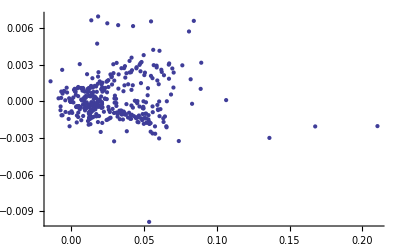

```mathematica
ListPlot[mfsRow[{"T","Y"}]]
```

Or we might take the scalar product of the X and PX columns

```mathematica
"X"."PX"/.qprules
```

-0.000266689

or form a matrix

```mathematica
({{"E11", "E12"}, {"E21", "E22"}})/.qprules//MatrixForm
```

(5.25333 | -3.43415×10^-17
0.0115639 | 0.190233)

Rather than continue with furthere illustrative examples, it is better to recommend that the user becomes familiar with standard Mathematica rule operations so that he can easily do what he wants himself.

The example contains tracking data for 16 particles so there are 16 X values for turn 0, for turn 1, etc. (until some particles are lost):

```mathematica
Take["TURNS"/.qprules,18]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}

```mathematica
Take["X"/.qprules,18]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00504514,0.00506582}

We can plot them against turn number with

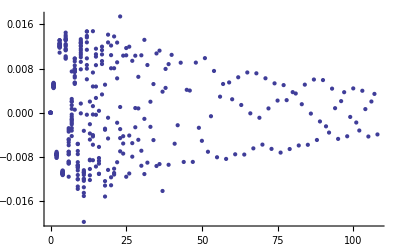

```mathematica
ListPlot[Transpose[{"TURNS","X"}/.qprules]]
```

Notice however that there is a common problem with MAD8 and MAD-X.  Sometimes the same name is used for a quantity in the header block and for one of the columns, e.g., "NAME" is used for the type of table and for the name of elements in MAD-X.  To avoid duplicate rules, the header item is changed as explained in the usage message

```mathematica
?mfsToRules
```

mfsToRules[mfsdata] transforms an mfs object into a list of rules for all the strings appearing in mfsKeyNames[mfsdata] and mfsColumnNames[mfsdata].  If the argument is a string, it is taken to be the name of a TFS file.  Where there are clashes, names from mfsKeyNames[mfsdata] have "_KEY" appended to them.
mfsToRules[mfsdata,elname] returns a list of rules for the values of all the columns at the element with NAME elname.
The form mfsToRules[mfsdata,elname,{cola,colb,...} generates rules only for the specified columns.

To get a list of all the strings for which rules are available, one can take the first element (since the list of rules is flat).

```mathematica
First/@qprules
```

{TYPE,XC,PXC,YC,PYC,ET,EY,EX,E11,E12,E13,E14,E15,E16,E21,E22,E23,E24,E25,E26,E31,E32,E33,E34,E35,E36,E41,E42,E43,E44,E45,E46,E51,E52,E53,E54,E55,E56,E61,E62,E63,E64,E65,E66,TITLE,ORIGIN,DATE,TIME,Source_File,TURNS,PARTICLE,X,PX,Y,PY,T,PT}

This problem does not arise with data from MAD Version 9 where the names for quantities are carefully chosen and unique (closed orbit components are called XC, PXC, ...).

If the argument to mfsToRules is a string, then it is interpreted as the name of a TFS file.  Thus we could have   generated the key and column variables directly  without assigning the mfs object qpmfs by typing  simply

```mathematica
mfsToRules[sampleFile]//Short
```

{TYPE→TRACK,«55»,PT→{0.,0.,«377»,-0.00158017}}

which is equivalent to

```mathematica
mfsToRules[tfsRead[sampleFile]]//Short
```

{TYPE→TRACK,«55»,PT→{0.,0.,«377»,-0.00158017}}

Additional arguments to mfsToRules provide an easy way to get hold of optical function values at a named element

```mathematica
mfsToRules[fodoTwiss,"QDHALF"]
```

mfsToRules[fodoTwiss,QDHALF]

```mathematica
mfsToRules[fodoTwiss,"JJJ"]//InputForm
```

mfsToRules::missingElement: element "JJJ" not found in mfs object.

$Failed

```mathematica
mfsToRules[fodoTwiss,"QDHALF",{"YC","foo","BETX","JUNK"}]
```

mfsToRules::missingColumns: column(s) {"foo", "JUNK"} not found in mfs object.

{BETX→7.46517,YC→0}

### More general usage of the package

#### Extracting header information from an mfs object

In this example, the TFS file contained a TRACK table from MAD.  The header block of the file contains various descriptors that are converted into keys and associated values in the mfs data object. To find out what they are we can evaluate

```mathematica
mfsKeyNames[qpmfs]
```

{TYPE,XC,PXC,YC,PYC,ET,EY,EX,E11,E12,E13,E14,E15,E16,E21,E22,E23,E24,E25,E26,E31,E32,E33,E34,E35,E36,E41,E42,E43,E44,E45,E46,E51,E52,E53,E54,E55,E56,E61,E62,E63,E64,E65,E66,TITLE,ORIGIN,DATE,TIME,Source_File}

The function mfsKeyValue can be used to extract the values corresponding to the keys:

```mathematica
ϵ = mfsKeyValue[qpmfs,"EX"]
```

2.98257×10^-8

```mathematica
mfsKeyValue[qpmfs,"ORIGIN"]
```

MAD 8.21/11 RS6000 - AIX

If a key does not exist, an error message will be given and a Null value returned.

```mathematica
mfsKeyValue[qpmfs,"QX"]
```

mfsKeyValue::notfound: Descriptor "QX" not found.

Lists can be extracted with one call, e.g,  to get four components of the closed orbit

```mathematica
mfsKeyValue[qpmfs,{"XC","PXC","YC","PYC"}]
```

{-0.000388354,-0.0000167029,-0.000381844,-2.94935×10^-6}

Of course, lists can be used in many ways in Mathematica.

```mathematica
ArcTan @@ mfsKeyValue[qpmfs,{"XC","PXC"}]
```

-3.09861

#### Extracting column information from an mfs object

The body of the original TFS file contained columns of data.  To find out what these are we use:

```mathematica
mfsColumnNames[qpmfs]
```

{TURNS,PARTICLE,X,PX,Y,PY,T,PT}

To extract columns of data we can use the function mfsColumn

```mathematica
?mfsColumn
```

mfsColumn[mfsdata,colname] returns the column of data labelled by the string colname in an mfs (or related) data object. A list of colnames may also be given to return a set of columns.  If colname is absent the entire block of columns is returned.

Thus, for example, we can get a list of all the values of the momentum PY.  Since this is long, we abbreviate the printing with the function Short:

```mathematica
Short[   mfsColumn[qpmfs,"PY"]   ,8]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000217497,0.0000214652,«344»,-0.0000133607,-0.0000464832,-0.0000369869,0.0000155165,0.000038503,0.00001693,-0.00001942,-0.0000366784,-0.0000171618,0.0000266039,0.0000343572,-3.51693×10^-6,-0.0000327806,-0.0000123483,0.000017505,0.0000320125,0.0000178347,-0.0000214404}

Multiple columns can also be returned.  Using Transpose, these can be transformed into lists of coordinate vectors.  Here are the coordinate pairs in the horizontal phase plane (abbreviated again)

```mathematica
Short[ xpx =Transpose[mfsColumn[qpmfs,{"X","PX"}]] ,10]
```

{{0.,0.0005},{0.,0.0005},{0.,0.0005},{0.,0.0005},{0.,0.0005},{0.,0.0005},{0.,0.0005},{0.,0.0005},{0.,0.0005},{0.,0.0005},{0.,0.0005},{0.,0.0005},«357»,{-0.00423936,-0.0000941761},{-0.000741994,0.000165904},{0.00441111,-6.78022×10^-6},{-0.00175107,-0.000149943},{-0.00319526,0.000113019},{0.00398775,0.0000855205},{0.000672365,-0.000142523},{-0.00427998,0.0000203029},{0.00204503,0.000155579},{0.00341965,-0.000114564},{-0.0039068,-0.0000886172}}

which is just what is needed for the standard ListPlot function.  Note that this example mixes the trajectories of all the  particles in the file (the TrackTable package deals with this in a better way)

In 2008, the function mfsRow was introduced to avoid the Transpose step so we could write the above as

```mathematica
Short[ xpx =mfsRow[qpmfs,{"X","PX"}] ,10]
```

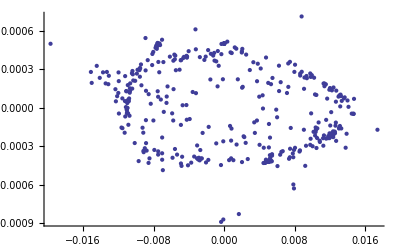

```mathematica
ListPlot[xpx]
```

Non-existent columns return Null

```mathematica
mfsColumn[qpmfs,"PXN"]
```

mfsColumn::notfound: Column "PXN" not found.

Finally, calling mfsColumn with only one argument returns a list containing all the columns (the entire "body" of the original data file).

```mathematica
Short[mfsColumn[qpmfs],10]
```

{{0,1,0.,0.0005,0.,0.,0.,0.},{0,2,0.,0.0005,0.,0.,0.,0.},{0,3,0.,0.0005,0.,0.,0.,0.},{0,4,0.,0.0005,0.,0.,0.,0.},«373»,{106,3,0.00204503,0.000155579,0.000287351,0.0000320125,-0.00656549,-0.000508005},{107,3,0.00341965,-0.000114564,0.000730013,0.0000178347,-0.00252763,-0.00143335},{108,3,-0.0039068,-0.0000886172,0.000805955,-0.0000214404,0.00293916,-0.00158017}}

The dimensions of this show us that there were 380 "lines" containing the 8 items specified by mfsColumnNames[qpmfs] above.

```mathematica
Dimensions[mfsColumn[qpmfs]]
```

{380,8}

#### Calculations using column information from an mfs object

Suppose that we would like to form the product of all the X and PX values in the mfs object qpmfs.

In the plotting example above, it was necessary to apply Transpose to the result of mfsColumn[qpmfs,{"X","PX"}] to transform the pair of long lists of X and PX values into a long list of pairs {X,PX} as required by ListPlot.  Having done this, it is easy to form, say, the product of all the X and PX values by mapping an appropriate pure function over the list.  Here is one which forms the product of X and PX

```mathematica
xpxprod1=(#1⟦1⟧ #1⟦2⟧&)/@xpx;
```

Viewing the result in abbreviated form,

```mathematica
Short[xpxprod1,5]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«358»,3.99246×10^-7,-1.231×10^-7,-2.99083×10^-8,2.62561×10^-7,-3.61125×10^-7,3.41034×10^-7,-9.58275×10^-8,-8.6896×10^-8,3.18164×10^-7,-3.91769×10^-7,3.4621×10^-7}

You may find it easier to do this in one step using MapThread.

```mathematica
xpxprod2=MapThread[Times,mfsColumn[qpmfs,{"X","PX"}]];
```

```mathematica
xpxprod1==xpxprod2
```

True

If this seems complicated, remember that we are using a simple example to illustrate general mechanisms.  The same result could be  achieved with

```mathematica
xpxprod3=mfsColumn[qpmfs,"X"]  mfsColumn[qpmfs,"PX"];
```

```mathematica
xpxprod3==xpxprod1
```

True

Even more simply,  in the approach using mfsInterpret, the same result could be achieved with

```mathematica
xpxprod4= X PX;
```

which is again equivalent

```mathematica
xpxprod4==xpxprod1
```

PX X=={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.13603×10^-6,-2.11042×10^-6,-1.98783×10^-6,-2.26439×10^-6,-2.01861×10^-6,-2.2175×10^-6,-2.15844×10^-6,-2.04026×10^-6,-2.09827×10^-6,-2.07938×10^-6,-1.98842×10^-6,-1.97409×10^-6,-2.18045×10^-6,-2.0881×10^-6,-2.0062×10^-6,-1.92911×10^-6,-3.71248×10^-6,-3.63421×10^-6,-3.50474×10^-6,-3.63394×10^-6,-3.77638×10^-6,-3.81241×10^-6,-3.63566×10^-6,-3.63671×10^-6,-3.40901×10^-6,-3.6722×10^-6,-3.75703×10^-6,-3.5455×10^-6,-3.7254×10^-6,-3.49539×10^-6,-3.67291×10^-6,-3.73054×10^-6,-2.66547×10^-6,-2.11855×10^-6,-2.28949×10^-6,-2.38082×10^-6,-2.44067×10^-6,-2.7591×10^-6,-2.62062×10^-6,-2.50955×10^-6,-2.0428×10^-6,-2.84624×10^-6,-2.62618×10^-6,-2.3993×10^-6,-2.61092×10^-6,-1.87585×10^-6,-2.79827×10^-6,-2.90956×10^-6,-1.44164×10^-6,1.79563×10^-7,-5.75701×10^-7,-3.88128×10^-7,-6.43661×10^-7,-1.54755×10^-6,-1.25049×10^-6,-7.73451×10^-7,4.82957×10^-7,-1.92114×10^-6,-1.61179×10^-6,-5.45829×10^-7,-1.41319×10^-6,4.96836×10^-7,-2.01741×10^-6,-2.80471×10^-6,1.3456×10^-6,2.38428×10^-6,1.95357×10^-6,2.12638×10^-6,2.10193×10^-6,1.24495×10^-6,1.65121×10^-6,1.83799×10^-6,2.60783×10^-6,7.86041×10^-7,1.19281×10^-6,2.14561×10^-6,1.09866×10^-6,2.52369×10^-6,7.06783×10^-7,-6.74687×10^-7,2.94446×10^-6,1.14033×10^-6,2.55028×10^-6,1.82417×10^-6,2.13248×10^-6,2.8551×10^-6,2.50365×10^-6,2.28709×10^-6,1.21596×10^-6,3.08799×10^-6,2.74177×10^-6,1.95461×10^-6,3.17112×10^-6,1.2955×10^-6,2.45088×10^-6,1.8471×10^-6,8.8648×10^-7,-1.67202×10^-6,3.13856×10^-7,-8.32426×10^-7,-1.46067×10^-6,-8.14299×10^-7,-1.30073×10^-7,-4.80592×10^-7,-1.08571×10^-6,9.47056×10^-7,-3.15366×10^-7,-5.03254×10^-7,6.35555×10^-7,-6.31428×10^-7,1.03559×10^-6,2.66839×10^-6,-2.0354×10^-6,-2.76122×10^-6,-2.25866×10^-6,-3.03606×10^-6,-2.83403×10^-6,-2.37934×10^-6,-2.39833×10^-6,-2.88612×10^-6,-2.92822×10^-6,-2.0526×10^-6,-2.61475×10^-6,-2.78453×10^-6,-2.33413×10^-6,-2.93803×10^-6,-1.97426×10^-6,-2.3224×10^-7,-2.94696×10^-6,-3.78427×10^-6,-2.62945×10^-6,-2.45042×10^-6,-3.70729×10^-6,-1.37697×10^-6,-2.76335×10^-6,-2.65996×10^-6,-2.97572×10^-6,-3.1797×10^-6,-3.29252×10^-6,-2.93164×10^-6,-2.90235×10^-6,-2.33674×10^-6,-2.58888×10^-6,-2.1111×10^-6,-2.79555×10^-6,-1.38813×10^-6,-1.47441×10^-6,-3.29774×10^-6,7.94823×10^-8,1.11797×10^-6,-2.3418×10^-6,-4.17761×10^-6,-2.15435×10^-6,-3.34136×10^-6,-4.70752×10^-6,-2.64561×10^-6,-1.77669×10^-6,-2.78811×10^-6,-1.67809×10^-6,-3.02189×10^-6,-2.54194×10^-6,5.46434×10^-7,-2.69551×10^-6,-9.81562×10^-6,-6.07382×10^-7,-1.98431×10^-6,6.77304×10^-7,-4.71071×10^-6,-6.52942×10^-7,-2.90161×10^-6,-1.38909×10^-6,7.71961×10^-7,-2.47405×10^-6,-2.82893×10^-6,2.35757×10^-6,-6.83309×10^-7,1.69002×10^-6,-2.75987×10^-6,2.22437×10^-6,1.90319×10^-6,3.06182×10^-7,9.89021×10^-7,2.29361×10^-6,-7.21415×10^-7,-1.08521×10^-6,1.60212×10^-6,2.79999×10^-6,3.34928×10^-6,-8.6124×10^-7,2.19542×10^-6,3.69659×10^-6,8.77736×10^-7,2.207×10^-6,1.01258×10^-6,-1.72467×10^-6,1.85958×10^-6,5.67863×10^-7,-9.01465×10^-7,-1.77309×10^-6,-1.4926×10^-7,-2.10994×10^-6,2.50784×10^-6,4.04205×10^-6,-1.91297×10^-6,-1.07559×10^-6,-1.9242×10^-6,-1.70918×10^-6,-2.86777×10^-6,-1.10263×10^-6,1.59521×10^-7,1.86529×10^-7,3.14053×10^-8,-2.71218×10^-6,-3.21296×10^-6,4.07423×10^-7,1.79127×10^-6,-2.44838×10^-6,2.30902×10^-6,-2.45157×10^-6,-2.84072×10^-6,2.46593×10^-6,1.17594×10^-6,-2.49483×10^-6,1.11844×10^-6,-4.20827×10^-6,-1.77436×10^-6,9.02392×10^-7,-1.57583×10^-6,-2.40581×10^-6,-1.79336×10^-6,9.13312×10^-8,-3.21528×10^-7,-2.18585×10^-6,-3.29373×10^-6,-1.80521×10^-6,1.80678×10^-6,-2.51958×10^-6,-4.25594×10^-7,-3.25379×10^-6,-4.93542×10^-8,2.69603×10^-6,-2.11232×10^-6,1.45158×10^-6,-4.31024×10^-6,2.14236×10^-6,7.30241×10^-7,5.89678×10^-7,2.0375×10^-6,-4.84625×10^-6,1.1879×10^-6,-1.80727×10^-6,3.38929×10^-6,-4.30798×10^-7,-2.99872×10^-6,-1.64722×10^-6,-2.24145×10^-6,-2.24751×10^-6,-2.03249×10^-6,-1.97255×10^-6,-8.33972×10^-7,8.25696×10^-7,2.41226×10^-8,1.66942×10^-6,1.84417×10^-6,2.15627×10^-6,2.61117×10^-6,-1.59887×10^-6,1.03595×10^-6,3.681×10^-7,1.06463×10^-6,-1.81098×10^-6,-2.24113×10^-6,-3.14154×10^-7,-1.60479×10^-6,-2.30607×10^-6,2.25735×10^-7,1.65897×10^-7,1.26975×10^-7,-3.99669×10^-7,2.16263×10^-6,2.84596×10^-6,1.00088×10^-6,8.62193×10^-7,-1.81838×10^-6,-1.92577×10^-6,-1.23598×10^-6,-2.81471×10^-6,1.4487×10^-6,-2.67594×10^-6,1.30867×10^-6,-3.28069×10^-6,-1.40638×10^-6,-4.99427×10^-6,-1.63655×10^-6,6.25556×10^-6,1.03578×10^-6,1.79897×10^-6,-8.34246×10^-7,-1.55965×10^-6,8.64718×10^-7,1.26791×10^-6,-1.16597×10^-6,-1.16486×10^-6,1.33343×10^-6,8.93719×10^-7,-1.49635×10^-6,-4.39953×10^-7,1.63748×10^-6,-2.00818×10^-7,-1.19642×10^-6,8.02953×10^-7,8.55867×10^-7,-1.21648×10^-6,-2.52907×10^-7,1.27128×10^-6,-6.71947×10^-7,-6.3615×10^-7,1.27604×10^-6,-4.06894×10^-7,-9.63496×10^-7,1.18036×10^-6,2.50746×10^-8,-1.06267×10^-6,8.15104×10^-7,2.4883×10^-7,-8.27786×10^-7,8.0765×10^-7,-2.04225×10^-7,-5.64463×10^-7,9.74964×10^-7,-4.94727×10^-7,-4.55224×10^-7,9.66186×10^-7,-5.25681×10^-7,-2.43206×10^-7,7.70327×10^-7,-6.875×10^-7,2.62063×10^-7,3.43727×10^-7,-6.47979×10^-7,5.78584×10^-7,-3.07234×10^-8,-4.50863×10^-7,6.5931×10^-7,-3.42843×10^-7,-9.19166×10^-8,4.80714×10^-7,-4.35474×10^-7,4.20424×10^-7,-1.36744×10^-7,-8.81732×10^-8,3.42927×10^-7,-3.7342×10^-7,3.99246×10^-7,-1.231×10^-7,-2.99083×10^-8,2.62561×10^-7,-3.61125×10^-7,3.41034×10^-7,-9.58275×10^-8,-8.6896×10^-8,3.18164×10^-7,-3.91769×10^-7,3.4621×10^-7}

#### Extracting row information from an mfs object (NEW in Nov 2008)

This is a bit shorter (although it executes a little more slowly)  to use where we formerly used Transpose[mfsColumn[...]]

```mathematica
Take[mfsRow[qpw,{"NAME","S","BETX"}],10]//TableForm
```

S.DS.L1.B1 | 12782.4 | 31.4155
DRIFT_89 | 12782.9 | 30.9103
BPM.13L1.B1 | 12782.9 | 30.9103
DRIFT_120 | 12783.5 | 30.3618
MQT.13L1.B1 | 12783.8 | 30.0783
DRIFT_121 | 12784.1 | 29.835
MQ.13L1.B1 | 12787.2 | 30.1201
DRIFT_70 | 12787.4 | 30.2806
MS.13L1.B1 | 12787.7 | 30.6578
DRIFT_64 | 12787.8 | 30.7448

However the second argument can take more general forms

```mathematica
?mfsRow
```

mfsRow[qp,template] returns a list of values of the template for each row of the mfs object qp; the template is an expression whose lowest level elements are strings belonging to the set of column names in qp, e.g, {"NAME",{"BETX",Cos["MUX"]} is valid but {"NAME",{"BETX",1+Cos["MUX"]} is not. Some further forms (e.g., {"NAME",{foo["BETX"],Cos["MUX"]} where no evaluation is defined for the symbol foo) may also work.
mfsRow[qp] returns a simple list of all column values for each row.

```mathematica
mfsColumnNames[qpw]
```

{KEYWORD,NAME,PARENT,L,K0L,K1L,K2L,K3L,S,BETX,BETY,DX,DY,XC,YC,ALFX,ALFY,MUX,MUY,DPX,PXC,PYC}

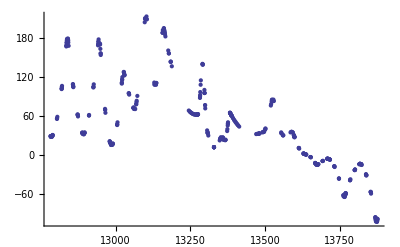

```mathematica
mfsRow[qpw,{"S","BETX"Cos["MUX"]}]//ListPlot
```

However not everything works

```mathematica
mfsRow[qpw,{"S",{{"BETX",-"ALFX"},{"BETY",-"ALFY"}}}]
```

mfsRow::invalid: invalid lowest level elements in template: {-1, -1}

$Failed

There are ways around the limitations using dummy symbols as heads

```mathematica
Take[
mfsRow[qpw,{"S",MatrixForm[{{"BETX",minus["ALFX"]},{"BETY",minus["ALFY"]}}]}]/.minus[x_]->-x,
6]
```

{{12782.4,(31.4155 | -0.515246
172.206 | 2.34716)},{12782.9,(30.9103 | -0.495105
174.563 | 2.36606)},{12782.9,(30.9103 | -0.495105
174.563 | 2.36606)},{12783.5,(30.3618 | -0.472265
177.258 | 2.38749)},{12783.8,(30.0783 | -0.413956
178.704 | 2.12964)},{12784.1,(29.835 | -0.40235
179.976 | 2.13887)}}

### Selection within mfs objects

Many of the tables saved by MAD take the form of a list of machine elements together with the values of various optical functions (e.g., the OPTICS, TWISS3, ENVELOPE tables).   Although MAD itself provides a selection mechanism for limiting these tables to certain classes of elements, it is often convenient to select further after the optics calculations have been done.  You might want to simply tabulate the functions at some known subset of the elements originally chosen.  Or, more interestingly, you might want to select elements according to the values of the optical functions.   For example, elements with large β functions might be potential  aperture limits.

In the following we provide a general selection mechanism and some simpler ones for common cases.

#### An OPTICS table example

Create an mfs data object from an OPTICS table containing values at the IPs and pickups in LEP:

```mathematica
opticsfile  = ToFileName[{AfsHomeDirectory["jowett"],"public","math","Madtomma","Mfs","Examples"},"OPTICSdp0000.tfs"]
```

P:\cern.ch\user\j\jowett\public\math\Madtomma\Mfs\Examples\OPTICSdp0000.tfs

```mathematica
OPTICS[0]=tfsRead[opticsfile,mfsVerbose->False];
```

```mathematica
mfsColumnNames[OPTICS[0]]
```

{NAME,BETX,DX,BETY}

#### General Selection Method

mfsSelect is a very general selection function modelled on the standard Mathematica function Select [1].  To understand how it works, you should first have some understanding of Select and the notion of pure functions in Mathematica.  If you do not, then I recommend that you skip this subsection and look at the simpler  selection functions (mfsMember, mfsRange) below.  They cover many practical cases.

```mathematica
?mfsSelect
```

mfsSelect[mfsdata,criterion] extracts rows satisfying criterion (function) from an mfsdata object.

mfsSelect is usually used in conjunction with an auxiliary function mfsColumnValue.  This allows selection from a specified row. To see how it works, we can look at the row number 14 in the OPTICS table.  This function can be used to extract the value of the column "NAME" for that row.

```mathematica
arow=mfsColumn[OPTICS[0]]⟦14⟧
```

{PU.QL15.R1,129.71,0.987151,21.1482}

```mathematica
mfsColumnValue[OPTICS[0],arow,"NAME"]
```

PU.QL15.R1

Now the mfsColumnValue function allows a very convenient specification of a selection criterion,  . For example, using it to construct an appropriate pure function, you can create a new mfs data object containing only the elements where β_x>250 :

```mathematica
hibetx=mfsSelect[OPTICS[0],(mfsColumnValue[OPTICS[0],#,"BETX"]>250.)&];
```

Then we can make a table showing the values of both β_x and β_y at these elements:

```mathematica
Transpose[mfsColumn[hibetx,{"NAME","BETX","BETY"}]]//TableForm
```

PU.QS1A.L2 | 294.131 | 70.5863
PU.QS1A.R2 | 294.136 | 70.5862
PU.QS1A.L4 | 321.516 | 74.436
PU.QS1A.R4 | 321.519 | 74.4358
PU.QS1A.L6 | 299.147 | 76.797
PU.QS1A.R6 | 299.145 | 76.7969
PU.QS1A.L8 | 321.465 | 74.4562
PU.QS1A.R8 | 321.467 | 74.4614

As a further example, we can select all the rows whose name contains the string QL11.  The similarity to the mechanism used in Select should now be very obvious.

```mathematica
TableForm[Transpose[mfsColumn[mfsSelect[OPTICS[0],StringMatchQ[mfsColumnValue[OPTICS[0],#1,"NAME"],"*QL11*"]&],{"NAME","BETX","DX"}]]]
```

PU.QL11.R1 | 146.035 | 7.4742×10^-9
PU.QL11.L3 | 146.041 | -2.42813×10^-7
PU.QL11.R3 | 146.041 | 2.34022×10^-7
PU.QL11.L5 | 146.042 | 2.01702×10^-7
PU.QL11.R5 | 146.042 | -1.78043×10^-7
PU.QL11.L7 | 146.041 | -1.20652×10^-7
PU.QL11.R7 | 146.041 | 8.66908×10^-8
PU.QL11.L1 | 146.036 | 2.46937×10^-8

Arbitrary logical cominations of criteria can be built up using standard Mathematica functions and operators.  Here, we select those elements containing "QS1" in their names where β_x>320:

```mathematica
mfsSelect[OPTICS[0],StringMatchQ[mfsColumnValue[OPTICS[0],#1,"NAME"],"*QS1*"]&&mfsColumnValue[OPTICS[0],#1,"BETX"]>320.&]
```

mfs[{{GAMTR,73.4237},{ALFA,0.000185493},{XIY,0.987098},{XIX,1.00236},{QY,76.1942},{QX,90.2859},{CIRCUM,26658.9},{DELTA,0.},{TYPE,OPTICS},{TITLE,N0520P97v2.lep, 90/60 BT optics for 1997 up to 97 GeV},{ORIGIN,MAD 8.21/13 HP/UX},{DATE,12/08/97},{TIME,15.04.39},{Source_File,P:\cern.ch\user\j\jowett\public\math\Madtomma\Mfs\Examples\OPTICSdp0000.tfs}},{NAME,BETX,DX,BETY},{{PU.QS1A.L4,321.516,-2.47388×10^-7,74.436},{PU.QS1A.R4,321.519,6.39189×10^-8,74.4358},{PU.QS1A.L8,321.465,-3.40013×10^-7,74.4562},{PU.QS1A.R8,321.467,3.03216×10^-7,74.4614}}]

If you know the internal structure of the mfs data object, you can refer directly to its elements  without using the mfsColumnValue function directly (but this is not normally recommended). For instance, knowing the columns 2 and 2 contain the appropriate quantities you can select the rows where β_xD_x>140:

```mathematica
result=mfsSelect[OPTICS[0],#1⟦2⟧ #1⟦3⟧>140.&];
```

```mathematica
Transpose[mfsColumn[result,{"NAME","BETX","DX"}]]//TableForm
```

PU.QS15.L2 | 149.927 | 0.950618
PU.QS15.R2 | 149.922 | 0.950618

This is equivalent to the selection

```mathematica
result1=mfsSelect[OPTICS[0],(mfsColumnValue[OPTICS[0],#,"BETX"]mfsColumnValue[OPTICS[0],#,"DX"]>140.)&];
```

#### Simple selection mechanisms

Common cases can be handled with simpler functions, e.g., when the names in a given column belongs to a specified set or numerical values fall in a given range.

To select from a set, we can first create a set of interaction point names and then select all the rows containing them.

```mathematica
IPs ={"IP2","IP4","IP6","IP8"};
```

```mathematica
IPoptics=mfsMember[OPTICS[0],"NAME",IPs]
```

mfs[{{GAMTR,73.4237},{ALFA,0.000185493},{XIY,0.987098},{XIX,1.00236},{QY,76.1942},{QX,90.2859},{CIRCUM,26658.9},{DELTA,0.},{TYPE,OPTICS},{TITLE,N0520P97v2.lep, 90/60 BT optics for 1997 up to 97 GeV},{ORIGIN,MAD 8.21/13 HP/UX},{DATE,12/08/97},{TIME,15.04.39},{Source_File,P:\cern.ch\user\j\jowett\public\math\Madtomma\Mfs\Examples\OPTICSdp0000.tfs}},{NAME,BETX,DX,BETY},{{IP2,2.,2.87934×10^-8,0.0499991},{IP4,2.00002,-2.57651×10^-8,0.0499995},{IP6,2.00002,1.76834×10^-8,0.0500001},{IP8,1.99995,-5.16881×10^-9,0.0499975}}]

```mathematica
Transpose[mfsColumn[IPoptics,{"NAME","BETX","BETY"}]]//TableForm
```

IP2 | 2. | 0.0499991
IP4 | 2.00002 | 0.0499995
IP6 | 2.00002 | 0.0500001
IP8 | 1.99995 | 0.0499975

A similar function handles the case when a value is a number in a specified range. For instance, select the rows with 120<β_x<126 :

```mathematica
betxval=mfsRange[OPTICS[0],"BETX",{120,126}] ;
```

```mathematica
Transpose[mfsColumn[betxval,{"NAME","BETX"}]]//TableForm
```

PU.QL2B.R1 | 125.212
PU.QL2B.L3 | 125.213
PU.QL2B.R3 | 125.21
PU.QL2B.L5 | 125.212
PU.QL2B.R5 | 125.211
PU.QL2B.L7 | 125.21
PU.QL2B.R7 | 125.213
PU.QL2B.L1 | 125.209

Of course, the limits of the range need not be finite.  To find all places with β_x>300, we can use

```mathematica
hibetx=mfsRange[OPTICS[0],"BETX",{300,∞}] ;
```

```mathematica
mfsColumn[hibetx,"NAME"]
```

{PU.QS1A.L4,PU.QS1A.R4,PU.QS1A.L8,PU.QS1A.R8}

#### Other Selection Methods

mfsSelect is quite general and useful. However other methods of data selection are also possible. For instance, you can use BooleanSelect from the Statistics`DataManipulation` package (which is made available by the Mfs package). As an example, first construct a boolean array  that indicates all places where the product β_x D_x>120 .

```mathematica
test = Greater[#,120.]& /@ ( mfsColumn[OPTICS[0],"BETX"] mfsColumn[OPTICS[0],"DX"]  );
```

```mathematica
Short[test,5]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,«463»,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False}

Then get the rows where the product β_x D_x>120 .

```mathematica
?BooleanSelect
```

Madtomma`Mfs`Mfs`BooleanSelect

```mathematica
BooleanSelect[Transpose[ mfsColumn[OPTICS[0],{"NAME","BETX","DX"}]],test]
```

BooleanSelect[{{IP1,25.2426,8.78313×10^-8},{PU.QL1B.R1,75.9511,1.10743×10^-7},{PU.QL2B.R1,125.212,1.33995×10^-7},{PU.QL4B.R1,17.0004,-5.92225×10^-8},{PU.QL5.R1,148.59,-2.09735×10^-7},{PU.QL6.R1,43.6364,-1.14942×10^-7},{PU.QL7.R1,146.044,-1.84568×10^-7},{PU.QL8.R1,55.9802,-9.39521×10^-8},{PU.QL9.R1,146.039,-1.03753×10^-7},{PU.QL10.R1,55.9782,-3.26717×10^-8},{PU.QL11.R1,146.035,7.4742×10^-9},{PU.QL12.R1,43.2113,0.00951065},{PU.QL14.R1,8.51054,0.281133},{PU.QL15.R1,129.71,0.987151},{PU.QL16.R1,39.1902,0.568661},{PU.QL17.R1,117.425,1.07893},{PU.QL18.R1,26.5935,0.603865},{PU.QD20.R1,25.9668,0.597167},{PU.QD22.R1,25.9684,0.59725},{PU.QD24.R1,25.9692,0.59727},{PU.QD26.R1,25.9705,0.59727},{PU.QD28.R1,25.9692,0.59727},{PU.QD30.R1,25.9705,0.59727},{PU.QD32.R1,25.9692,0.59727},{PU.QD34.R1,25.9705,0.59727},{PU.QD36.R1,25.9692,0.59727},{PU.QD38.R1,25.9705,0.59727},{PU.QD40.R1,25.9692,0.59727},{PU.QD42.R1,25.9705,0.59727},{PU.QD44.R1,25.9692,0.59727},{PU.QD46.R1,25.9705,0.59727},{PU.QD48.R1,25.9692,0.59727},{PU.QD48.L2,25.9705,0.59727},{PU.QD46.L2,25.9692,0.59727},{PU.QD44.L2,25.9705,0.59727},{PU.QD42.L2,25.9692,0.59727},{PU.QD40.L2,25.9705,0.59727},{PU.QD38.L2,25.9692,0.59727},{PU.QD36.L2,25.9705,0.59727},{PU.QD34.L2,25.9692,0.59727},{PU.QD32.L2,25.9705,0.59727},{PU.QD30.L2,25.9692,0.59727},{PU.QD28.L2,25.9705,0.59727},{PU.QD26.L2,25.9692,0.59727},{PU.QD24.L2,25.9705,0.59727},{PU.QD22.L2,25.9692,0.59727},{PU.QD20.L2,25.9705,0.59727},{PU.QS18.L2,25.9692,0.59727},{PU.QS17.L2,99.7021,0.969197},{PU.QS16.L2,41.1536,0.540284},{PU.QS15.L2,149.927,0.950618},{PU.QS14.L2,8.55713,0.288718},{PU.QS12.L2,27.9648,0.0114436},{PU.QS11.L2,91.2109,-3.4675×10^-8},{PU.QS10.L2,7.85585,5.70614×10^-8},{PU.QS9.L2,130.1,1.82484×10^-7},{PU.QS8.L2,22.782,3.16583×10^-8},{PU.QS7.L2,86.3211,-5.43801×10^-8},{PU.QS6.L2,27.454,-6.99656×10^-8},{PU.QS5.L2,90.0553,-1.82243×10^-7},{PU.QS4.L2,17.4177,-2.58849×10^-8},{PU.QS3.L2,40.9498,-1.05204×10^-8},{PU.QS1A.L2,294.131,1.02048×10^-7},{PU.QS0.L2,40.0054,4.48462×10^-8},{IP2,2.,2.87934×10^-8},{PU.QS0.R2,40.0061,4.21249×10^-8},{PU.QS1A.R2,294.136,9.45253×10^-8},{PU.QS3.R2,40.9496,-1.34331×10^-8},{PU.QS4.R2,17.4174,-2.76953×10^-8},{PU.QS5.R2,90.0569,-1.80756×10^-7},{PU.QS6.R2,27.4547,-6.81399×10^-8},{PU.QS7.R2,86.3233,-5.02989×10^-8},{PU.QS8.R2,22.7817,3.37123×10^-8},{PU.QS9.R2,130.094,1.85661×10^-7},{PU.QS10.R2,7.85615,5.70268×10^-8},{PU.QS11.R2,91.2073,-3.89598×10^-8},{PU.QS12.R2,27.9644,0.0114436},{PU.QS14.R2,8.55696,0.288718},{PU.QS15.R2,149.922,0.950618},{PU.QS16.R2,41.1532,0.540284},{PU.QS17.R2,99.7042,0.969197},{PU.QS18.R2,25.9702,0.59727},{PU.QD20.R2,25.9696,0.59727},{PU.QD22.R2,25.9702,0.59727},{PU.QD24.R2,25.9696,0.59727},{PU.QD26.R2,25.9702,0.59727},{PU.QD28.R2,25.9696,0.59727},{PU.QD30.R2,25.9702,0.59727},{PU.QD32.R2,25.9696,0.59727},{PU.QD34.R2,25.9702,0.59727},{PU.QD36.R2,25.9696,0.59727},{PU.QD38.R2,25.9702,0.59727},{PU.QD40.R2,25.9696,0.59727},{PU.QD42.R2,25.9702,0.59727},{PU.QD44.R2,25.9696,0.59727},{PU.QD46.R2,25.9702,0.59727},{PU.QD48.R2,25.9696,0.59727},{PU.QD48.L3,25.9702,0.59727},{PU.QD46.L3,25.9696,0.59727},{PU.QD44.L3,25.9702,0.59727},{PU.QD42.L3,25.9696,0.59727},{PU.QD40.L3,25.9702,0.59727},{PU.QD38.L3,25.9696,0.59727},{PU.QD36.L3,25.9702,0.59727},{PU.QD34.L3,25.9696,0.59727},{PU.QD32.L3,25.9702,0.59727},{PU.QD30.L3,25.9696,0.59727},{PU.QD28.L3,25.9702,0.59727},{PU.QD26.L3,25.9696,0.59727},{PU.QD24.L3,25.9702,0.59727},{PU.QD22.L3,25.9696,0.59727},{PU.QD20.L3,25.9702,0.59727},{PU.QL18.L3,26.5917,0.603944},{PU.QL17.L3,117.415,1.07886},{PU.QL16.L3,39.1978,0.568597},{PU.QL15.L3,129.783,0.987148},{PU.QL14.L3,8.50772,0.28111},{PU.QL12.L3,43.2115,0.00951048},{PU.QL11.L3,146.041,-2.42813×10^-7},{PU.QL10.L3,55.9802,-1.37245×10^-7},{PU.QL9.L3,146.042,-1.86712×10^-7},{PU.QL8.L3,55.9802,-8.27258×10^-8},{PU.QL7.L3,146.041,-7.58813×10^-8},{PU.QL6.L3,43.6347,1.22517×10^-8},{PU.QL5.L3,148.595,9.16936×10^-8},{PU.QL4B.L3,17.0029,6.04301×10^-8},{PU.QL2B.L3,125.213,1.32513×10^-7},{PU.QL1B.L3,75.9377,9.44946×10^-8},{IP3,25.2416,-2.40027×10^-8},{PU.QL1B.R3,75.9361,-1.5258×10^-7},{PU.QL2B.R3,125.21,-2.02445×10^-7},{PU.QL4B.R3,17.0033,-2.71925×10^-8},{PU.QL5.R3,148.596,2.36161×10^-8},{PU.QL6.R3,43.6344,5.01969×10^-8},{PU.QL7.R3,146.038,1.7429×10^-7},{PU.QL8.R3,55.979,1.31958×10^-7},{PU.QL9.R3,146.039,2.39216×10^-7},{PU.QL10.R3,55.9797,1.52245×10^-7},{PU.QL11.R3,146.041,2.34022×10^-7},{PU.QL12.R3,43.2122,0.00951072},{PU.QL14.R3,8.50756,0.28111},{PU.QL15.R3,129.783,0.987147},{PU.QL16.R3,39.1984,0.568597},{PU.QL17.R3,117.418,1.07886},{PU.QL18.R3,26.5919,0.603944},{PU.QD20.R3,25.97,0.59727},{PU.QD22.R3,25.9698,0.59727},{PU.QD24.R3,25.97,0.59727},{PU.QD26.R3,25.9698,0.59727},{PU.QD28.R3,25.97,0.59727},{PU.QD30.R3,25.9698,0.59727},{PU.QD32.R3,25.97,0.59727},{PU.QD34.R3,25.9698,0.59727},{PU.QD36.R3,25.97,0.59727},{PU.QD38.R3,25.9698,0.59727},{PU.QD40.R3,25.97,0.59727},{PU.QD42.R3,25.9698,0.59727},{PU.QD44.R3,25.97,0.59727},{PU.QD46.R3,25.9698,0.59727},{PU.QD48.R3,25.97,0.59727},{PU.QD48.L4,25.9698,0.59727},{PU.QD46.L4,25.97,0.59727},{PU.QD44.L4,25.9698,0.59727},{PU.QD42.L4,25.97,0.59727},{PU.QD40.L4,25.9698,0.59727},{PU.QD38.L4,25.97,0.59727},{PU.QD36.L4,25.9698,0.59727},{PU.QD34.L4,25.97,0.59727},{PU.QD32.L4,25.9698,0.59727},{PU.QD30.L4,25.97,0.59727},{PU.QD28.L4,25.9698,0.59727},{PU.QD26.L4,25.97,0.59727},{PU.QD24.L4,25.9698,0.59727},{PU.QD22.L4,25.97,0.59727},{PU.QD20.L4,25.9698,0.59727},{PU.QS18.L4,25.97,0.59727},{PU.QS17.L4,91.4156,0.904504},{PU.QS16.L4,49.269,0.565283},{PU.QS15.L4,139.083,0.891688},{PU.QS14.L4,8.01018,0.275156},{PU.QS12.L4,20.0172,0.0116072},{PU.QS11.L4,89.1784,-9.44196×10^-8},{PU.QS10.L4,17.0369,-8.29976×10^-8},{PU.QS9.L4,107.639,-1.84119×10^-7},{PU.QS8.L4,8.48464,2.11101×10^-8},{PU.QS7.L4,148.581,2.31039×10^-7},{PU.QS6.L4,12.9968,6.84185×10^-8},{PU.QS5.L4,65.1719,-1.7628×10^-9},{PU.QS3A.L4,38.6852,-3.76497×10^-8},{PU.QS1A.L4,321.516,-2.47388×10^-7},{PU.QS0.L4,39.596,-9.22467×10^-8},{IP4,2.00002,-2.57651×10^-8},{PU.QS0.R4,39.5963,1.4911×10^-8},{PU.QS1A.R4,321.519,6.39189×10^-8},{PU.QS3A.R4,38.685,7.34487×10^-8},{PU.QS5.R4,65.1712,1.29728×10^-7},{PU.QS6.R4,12.9969,6.23764×10^-8},{PU.QS7.R4,148.583,6.80107×10^-8},{PU.QS8.R4,8.48462,-3.13361×10^-8},{PU.QS9.R4,107.639,-1.93446×10^-7},{PU.QS10.R4,17.0371,-4.00992×10^-8},{PU.QS11.R4,89.1785,7.61655×10^-8},{PU.QS12.R4,20.0169,0.0116073},{PU.QS14.R4,8.01025,0.275156},{PU.QS15.R4,139.082,0.891688},{PU.QS16.R4,49.2684,0.565283},{PU.QS17.R4,91.4149,0.904504},{PU.QS18.R4,25.9702,0.59727},{PU.QD20.R4,25.9695,0.59727},{PU.QD22.R4,25.9702,0.59727},{PU.QD24.R4,25.9695,0.59727},{PU.QD26.R4,25.9702,0.59727},{PU.QD28.R4,25.9695,0.59727},{PU.QD30.R4,25.9702,0.59727},{PU.QD32.R4,25.9695,0.59727},{PU.QD34.R4,25.9702,0.59727},{PU.QD36.R4,25.9695,0.59727},{PU.QD38.R4,25.9702,0.59727},{PU.QD40.R4,25.9695,0.59727},{PU.QD42.R4,25.9702,0.59727},{PU.QD44.R4,25.9695,0.59727},{PU.QD46.R4,25.9702,0.59727},{PU.QD48.R4,25.9695,0.59727},{PU.QD48.L5,25.9702,0.59727},{PU.QD46.L5,25.9695,0.59727},{PU.QD44.L5,25.9702,0.59727},{PU.QD42.L5,25.9695,0.59727},{PU.QD40.L5,25.9702,0.59727},{PU.QD38.L5,25.9695,0.59727},{PU.QD36.L5,25.9702,0.59727},{PU.QD34.L5,25.9695,0.59727},{PU.QD32.L5,25.9702,0.59727},{PU.QD30.L5,25.9695,0.59727},{PU.QD28.L5,25.9702,0.59727},{PU.QD26.L5,25.9695,0.59727},{PU.QD24.L5,25.9702,0.59727},{PU.QD22.L5,25.9695,0.59727},{PU.QD20.L5,25.9702,0.59727},{PU.QL18.L5,26.5917,0.603944},{PU.QL17.L5,117.417,1.07886},{PU.QL16.L5,39.1983,0.568597},{PU.QL15.L5,129.783,0.987147},{PU.QL14.L5,8.50762,0.28111},{PU.QL12.L5,43.212,0.00951074},{PU.QL11.L5,146.042,2.01702×10^-7},{PU.QL10.L5,55.9802,9.50881×10^-8},{PU.QL9.L5,146.041,9.89506×10^-8},{PU.QL8.L5,55.9796,1.92377×10^-8},{PU.QL7.L5,146.039,-3.28049×10^-8},{PU.QL6.L5,43.6355,-6.89246×10^-8},{PU.QL5.L5,148.585,-1.82266×10^-7},{PU.QL4B.L5,17.0016,-7.96134×10^-8},{PU.QL2B.L5,125.212,-3.92767×10^-8},{PU.QL1B.L5,75.9468,-2.02256×10^-8},{IP5,25.2415,6.45972×10^-8},{PU.QL1B.R5,75.9468,1.76556×10^-7},{PU.QL2B.R5,125.211,2.27479×10^-7},{PU.QL4B.R5,17.0016,-9.83156×10^-9},{PU.QL5.R5,148.585,-1.2805×10^-7},{PU.QL6.R5,43.6355,-9.91423×10^-8},{PU.QL7.R5,146.04,-2.33285×10^-7},{PU.QL8.R5,55.9804,-1.52085×10^-7},{PU.QL9.R5,146.041,-2.40252×10^-7},{PU.QL10.R5,55.9835,-1.32377×10^-7},{PU.QL11.R5,146.042,-1.78043×10^-7},{PU.QL12.R5,43.212,0.00951055},{PU.QL14.R5,8.50761,0.28111},{PU.QL15.R5,129.783,0.987148},{PU.QL16.R5,39.1983,0.568597},{PU.QL17.R5,117.417,1.07886},{PU.QL18.R5,26.5917,0.603944},{PU.QD20.R5,25.9702,0.59727},{PU.QD22.R5,25.9696,0.59727},{PU.QD24.R5,25.9702,0.59727},{PU.QD26.R5,25.9696,0.59727},{PU.QD28.R5,25.9702,0.59727},{PU.QD30.R5,25.9696,0.59727},{PU.QD32.R5,25.9702,0.59727},{PU.QD34.R5,25.9696,0.59727},{PU.QD36.R5,25.9702,0.59727},{PU.QD38.R5,25.9696,0.59727},{PU.QD40.R5,25.9702,0.59727},{PU.QD42.R5,25.9696,0.59727},{PU.QD44.R5,25.9702,0.59727},{PU.QD46.R5,25.9696,0.59727},{PU.QD48.R5,25.9702,0.59727},{PU.QD48.L6,25.9696,0.59727},{PU.QD46.L6,25.9702,0.59727},{PU.QD44.L6,25.9696,0.59727},{PU.QD42.L6,25.9702,0.59727},{PU.QD40.L6,25.9696,0.59727},{PU.QD38.L6,25.9702,0.59727},{PU.QD36.L6,25.9696,0.59727},{PU.QD34.L6,25.9702,0.59727},{PU.QD32.L6,25.9696,0.59727},{PU.QD30.L6,25.9702,0.59727},{PU.QD28.L6,25.9696,0.59727},{PU.QD26.L6,25.9702,0.59727},{PU.QD24.L6,25.9696,0.59727},{PU.QD22.L6,25.9702,0.59727},{PU.QD20.L6,25.9696,0.59727},{PU.QS18.L6,25.9702,0.59727},{PU.QS17.L6,118.596,1.10177},{PU.QS16.L6,37.4394,0.571651},{PU.QS15.L6,109.087,0.902138},{PU.QS14.L6,10.3385,0.289143},{PU.QS12.L6,21.676,0.0114441},{PU.QS11.L6,85.8298,1.31311×10^-7},{PU.QS10.L6,10.7726,6.45627×10^-8},{PU.QS9.L6,80.1496,7.65062×10^-8},{PU.QS8.L6,16.7796,-2.90955×10^-8},{PU.QS7.L6,87.4257,-1.59595×10^-7},{PU.QS6.L6,24.1883,-1.00072×10^-7},{PU.QS5.L6,91.3708,-1.6855×10^-7},{PU.QS4.L6,17.3124,4.72242×10^-8},{PU.QS3.L6,41.8943,9.61409×10^-8},{PU.QS1A.L6,299.147,3.26209×10^-7},{PU.QS0.L6,41.5873,1.24269×10^-7},{IP6,2.00002,1.76834×10^-8},{PU.QS0.R6,41.5865,-7.14487×10^-8},{PU.QS1A.R6,299.145,-2.0832×10^-7},{PU.QS3.R6,41.8944,-1.109×10^-7},{PU.QS4.R6,17.3125,-7.97352×10^-8},{PU.QS5.R6,91.3699,-5.28845×10^-8},{PU.QS6.R6,24.188,2.70062×10^-8},{PU.QS7.R6,87.4255,1.39648×10^-7},{PU.QS8.R6,16.7798,8.28844×10^-8},{PU.QS9.R6,80.1501,1.41574×10^-7},{PU.QS10.R6,10.7725,8.08094×10^-10},{PU.QS11.R6,85.8301,-1.63405×10^-7},{PU.QS12.R6,21.6762,0.011444},{PU.QS14.R6,10.3384,0.289143},{PU.QS15.R6,109.088,0.902138},{PU.QS16.R6,37.4398,0.571651},{PU.QS17.R6,118.596,1.10177},{PU.QS18.R6,25.97,0.59727},{PU.QD20.R6,25.9698,0.59727},{PU.QD22.R6,25.97,0.59727},{PU.QD24.R6,25.9698,0.59727},{PU.QD26.R6,25.97,0.59727},{PU.QD28.R6,25.9698,0.59727},{PU.QD30.R6,25.97,0.59727},{PU.QD32.R6,25.9698,0.59727},{PU.QD34.R6,25.97,0.59727},{PU.QD36.R6,25.9698,0.59727},{PU.QD38.R6,25.97,0.59727},{PU.QD40.R6,25.9698,0.59727},{PU.QD42.R6,25.97,0.59727},{PU.QD44.R6,25.9698,0.59727},{PU.QD46.R6,25.97,0.59727},{PU.QD48.R6,25.9698,0.59727},{PU.QD48.L7,25.97,0.59727},{PU.QD46.L7,25.9698,0.59727},{PU.QD44.L7,25.97,0.59727},{PU.QD42.L7,25.9698,0.59727},{PU.QD40.L7,25.97,0.59727},{PU.QD38.L7,25.9698,0.59727},{PU.QD36.L7,25.97,0.59727},{PU.QD34.L7,25.9698,0.59727},{PU.QD32.L7,25.97,0.59727},{PU.QD30.L7,25.9698,0.59727},{PU.QD28.L7,25.97,0.59727},{PU.QD26.L7,25.9698,0.59727},{PU.QD24.L7,25.97,0.59727},{PU.QD22.L7,25.9698,0.59727},{PU.QD20.L7,25.97,0.59727},{PU.QL18.L7,26.5919,0.603944},{PU.QL17.L7,117.418,1.07886},{PU.QL16.L7,39.1984,0.568597},{PU.QL15.L7,129.783,0.987148},{PU.QL14.L7,8.50755,0.28111},{PU.QL12.L7,43.2122,0.00951051},{PU.QL11.L7,146.041,-1.20652×10^-7},{PU.QL10.L7,55.9797,-3.39645×10^-8},{PU.QL9.L7,146.039,8.81553×10^-9},{PU.QL8.L7,55.979,4.84231×10^-8},{PU.QL7.L7,146.038,1.357×10^-7},{PU.QL6.L7,43.6344,1.12378×10^-7},{PU.QL5.L7,148.596,2.37538×10^-7},{PU.QL4B.L7,17.0033,8.32536×10^-8},{PU.QL2B.L7,125.21,-6.2257×10^-8},{PU.QL1B.L7,75.9359,-5.84817×10^-8},{IP7,25.2416,-9.27291×10^-8},{PU.QL1B.R7,75.9377,-1.65917×10^-7},{PU.QL2B.R7,125.213,-2.07908×10^-7},{PU.QL4B.R7,17.0029,4.51524×10^-8},{PU.QL5.R7,148.595,2.07935×10^-7},{PU.QL6.R7,43.6347,1.28878×10^-7},{PU.QL7.R7,146.041,2.44482×10^-7},{PU.QL8.R7,55.9803,1.41774×10^-7},{PU.QL9.R7,146.042,1.94022×10^-7},{PU.QL10.R7,55.9802,9.19148×10^-8},{PU.QL11.R7,146.041,8.66908×10^-8},{PU.QL12.R7,43.2115,0.00951061},{PU.QL14.R7,8.50772,0.28111},{PU.QL15.R7,129.783,0.987147},{PU.QL16.R7,39.1978,0.568597},{PU.QL17.R7,117.415,1.07886},{PU.QL18.R7,26.5917,0.603944},{PU.QD20.R7,25.9702,0.59727},{PU.QD22.R7,25.9696,0.59727},{PU.QD24.R7,25.9702,0.59727},{PU.QD26.R7,25.9696,0.59727},{PU.QD28.R7,25.9702,0.59727},{PU.QD30.R7,25.9696,0.59727},{PU.QD32.R7,25.9702,0.59727},{PU.QD34.R7,25.9696,0.59727},{PU.QD36.R7,25.9702,0.59727},{PU.QD38.R7,25.9696,0.59727},{PU.QD40.R7,25.9702,0.59727},{PU.QD42.R7,25.9696,0.59727},{PU.QD44.R7,25.9702,0.59727},{PU.QD46.R7,25.9696,0.59727},{PU.QD48.R7,25.9702,0.59727},{PU.QD48.L8,25.9696,0.59727},{PU.QD46.L8,25.9702,0.59727},{PU.QD44.L8,25.9696,0.59727},{PU.QD42.L8,25.9702,0.59727},{PU.QD40.L8,25.9696,0.59727},{PU.QD38.L8,25.9702,0.59727},{PU.QD36.L8,25.9696,0.59727},{PU.QD34.L8,25.9702,0.59727},{PU.QD32.L8,25.9696,0.59727},{PU.QD30.L8,25.9702,0.59727},{PU.QD28.L8,25.9696,0.59727},{PU.QD26.L8,25.9702,0.59727},{PU.QD24.L8,25.9696,0.59727},{PU.QD22.L8,25.9702,0.59727},{PU.QD20.L8,25.9696,0.59727},{PU.QS18.L8,25.9702,0.59727},{PU.QS17.L8,91.4137,0.904504},{PU.QS16.L8,49.268,0.565283},{PU.QS15.L8,139.082,0.891688},{PU.QS14.L8,8.01035,0.275156},{PU.QS12.L8,20.0168,0.0116072},{PU.QS11.L8,89.1795,-1.78083×10^-7},{PU.QS10.L8,17.0372,-5.66596×10^-8},{PU.QS9.L8,107.638,-2.81991×10^-8},{PU.QS8.L8,8.48469,5.31644×10^-8},{PU.QS7.L8,148.585,1.98414×10^-7},{PU.QS6.L8,12.9969,1.93501×10^-8},{PU.QS5.L8,65.1739,-1.23034×10^-7},{PU.QS3A.L8,38.6921,-1.11209×10^-7},{PU.QS1A.L8,321.465,-3.40013×10^-7},{PU.QS0.L8,39.5991,-1.18475×10^-7},{IP8,1.99995,-5.16881×10^-9},{PU.QS0.R8,39.5971,1.0296×10^-7},{PU.QS1A.R8,321.467,3.03216×10^-7},{PU.QS3A.R8,38.6935,1.18389×10^-7},{PU.QS5.R8,65.1769,1.48701×10^-7},{PU.QS6.R8,12.9965,6.88967×10^-9},{PU.QS7.R8,148.579,-1.3841×10^-7},{PU.QS8.R8,8.48496,-5.52126×10^-8},{PU.QS9.R8,107.636,-4.75453×10^-8},{PU.QS10.R8,17.0364,3.19619×10^-8},{PU.QS11.R8,89.1813,1.74411×10^-7},{PU.QS12.R8,20.0177,0.0116073},{PU.QS14.R8,8.01027,0.275156},{PU.QS15.R8,139.088,0.891688},{PU.QS16.R8,49.2698,0.565283},{PU.QS17.R8,91.4142,0.904504},{PU.QS18.R8,25.969,0.59727},{PU.QD20.R8,25.9708,0.59727},{PU.QD22.R8,25.969,0.59727},{PU.QD24.R8,25.9708,0.59727},{PU.QD26.R8,25.969,0.59727},{PU.QD28.R8,25.9708,0.59727},{PU.QD30.R8,25.969,0.59727},{PU.QD32.R8,25.9708,0.59727},{PU.QD34.R8,25.969,0.59727},{PU.QD36.R8,25.9708,0.59727},{PU.QD38.R8,25.969,0.59727},{PU.QD40.R8,25.9708,0.59727},{PU.QD42.R8,25.969,0.59727},{PU.QD44.R8,25.9708,0.59727},{PU.QD46.R8,25.969,0.59727},{PU.QD48.R8,25.9708,0.59727},{PU.QD48.L1,25.969,0.59727},{PU.QD46.L1,25.9708,0.59727},{PU.QD44.L1,25.969,0.59727},{PU.QD42.L1,25.9708,0.59727},{PU.QD40.L1,25.969,0.59727},{PU.QD38.L1,25.9708,0.59727},{PU.QD36.L1,25.969,0.59727},{PU.QD34.L1,25.9708,0.59727},{PU.QD32.L1,25.969,0.59727},{PU.QD30.L1,25.9708,0.59727},{PU.QD28.L1,25.969,0.59727},{PU.QD26.L1,25.9708,0.59727},{PU.QD24.L1,25.969,0.59727},{PU.QD22.L1,25.9686,0.59725},{PU.QD20.L1,25.9665,0.597167},{PU.QL18.L1,26.5938,0.603865},{PU.QL17.L1,117.428,1.07893},{PU.QL16.L1,39.1909,0.568661},{PU.QL15.L1,129.71,0.987151},{PU.QL14.L1,8.51035,0.281133},{PU.QL12.L1,43.2122,0.00951066},{PU.QL11.L1,146.036,2.46937×10^-8},{PU.QL10.L1,55.9776,-2.22177×10^-8},{PU.QL9.L1,146.036,-8.83716×10^-8},{PU.QL8.L1,55.9788,-8.61995×10^-8},{PU.QL7.L1,146.041,-1.75534×10^-7},{PU.QL6.L1,43.636,-1.13571×10^-7},{PU.QL5.L1,148.591,-2.12194×10^-7},{PU.QL4B.L1,17.0008,-6.23868×10^-8},{PU.QL2B.L1,125.209,1.21899×10^-7},{PU.QL1B.L1,75.9491,1.0182×10^-7},{ENDLEP,25.2426,8.78313×10^-8}},{False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False}]

Still another way to do this is to use MapThread to form the product of the two columns together with the element names.  Then the elements can be selected.

```mathematica
Select[MapThread[{#1,#2 #3}&,mfsColumn[OPTICS[0],{"NAME","BETX","DX"}]],Last[#1]>120.&]
```

{{PU.QL15.R1,128.043},{PU.QL17.R1,126.693},{PU.QS15.L2,142.523},{PU.QS15.R2,142.519},{PU.QL17.L3,126.674},{PU.QL15.L3,128.115},{PU.QL15.R3,128.115},{PU.QL17.R3,126.678},{PU.QS15.L4,124.019},{PU.QS15.R4,124.018},{PU.QL17.L5,126.677},{PU.QL15.L5,128.115},{PU.QL15.R5,128.115},{PU.QL17.R5,126.677},{PU.QS17.L6,130.666},{PU.QS17.R6,130.666},{PU.QL17.L7,126.678},{PU.QL15.L7,128.115},{PU.QL15.R7,128.115},{PU.QL17.R7,126.674},{PU.QS15.L8,124.018},{PU.QS15.R8,124.023},{PU.QL17.L1,126.697},{PU.QL15.L1,128.043}}

### Modifying and saving mfs objects

#### Modifying the header part of the object

It may be useful to add additional keys and values that were not given in the original TFS file. These can be any kind of object definable in Mathematica.

```mathematica
qpmfs=mfsAddKey[qpmfs,{"REMARK","Example for conference paper."}];
```

```mathematica
qpmfs=mfsAddKey[qpmfs,{"KICKVALUE",4×10^-3}];
```

```mathematica
qpmfs = mfsAddKey[qpmfs,{"AMATRIX",Inverse[({{σ, α}, {β, -σ^-1}})]}];
```

```mathematica
mfsKeyValue[qpmfs,"AMATRIX"]//MatrixForm
```

(-1/((-1-α β) σ) | -α/(-1-α β)
-β/(-1-α β) | σ/(-1-α β))

Descriptors can be changed with mfsEditKey as follows.  In this example, the COMMENT is empty since nothing was supplied in the MAD run:

```mathematica
mfsKeyValue[qpmfs,"COMMENT"]
```

mfsKeyValue::notfound: Descriptor "COMMENT" not found.

However it can be added as an afterthought:

```mathematica
qpmfs=mfsEditKey[qpmfs,{"COMMENT","Tracking from an initial kick."}];
```

mfsKeyValue::notfound: Descriptor "COMMENT" not found.

```mathematica
mfsKeyValue[qpmfs,"COMMENT"]
```

mfsKeyValue[Null,COMMENT]

Descriptors can be deleted with

```mathematica
qpmfs=mfsDeleteKey[qpmfs,"ET"];
```

The list of keys now reads

```mathematica
mfsKeyNames[qpmfs]
```

mfsKeyNames[mfsDeleteKey[Null,ET]]

#### Adding and removing columns

Let us show how to add another column of data to the mfs data object OPTICS[0].  An additional column should have length

```mathematica
collen=Length[Last[OPTICS[0]]]
```

509

Let us construct a simple index of the elements since this particular data object contains no azimuth "S"

```mathematica
idx=Range[collen] ;
```

```mathematica
OPTICS[1]=mfsAddColumn[OPTICS[0],"INDEX",idx];
```

Now there is a new column that we can use in a trivial way to produce a plot

```mathematica
mfsColumnNames[OPTICS[1]]
```

{BETX,BETY,DX,INDEX,NAME}

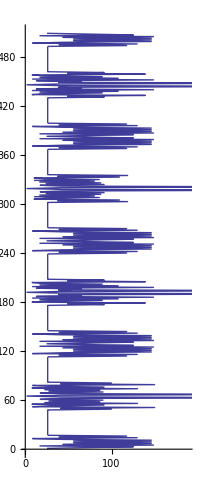

```mathematica
ListPlot[Transpose[mfsColumn[OPTICS[1],{"BETX","INDEX"}]],Joined->True,AspectRatio->Automatic]
```

There are also functions for removing keys and columns

```mathematica
nodx=mfsDeleteKey[ 
		mfsDeleteColumn[OPTICS[0],"DX"],
			"DELTA"];
```

```mathematica
nobetas= mfsDeleteColumn[OPTICS[0],{"BETX","BETY"}];
```

```mathematica
mfsKeyNames[nodx]
```

{GAMTR,ALFA,XIY,XIX,QY,QX,CIRCUM,TYPE,TITLE,ORIGIN,DATE,TIME,Source_File}

```mathematica
mfsColumnNames[nodx]
```

{NAME,BETX,BETY}

```mathematica
mfsColumnNames[nobetas]
```

{NAME,DX}

We shall use these reduced data objects in the next subsection.

#### Merging several mfs objects and making sure they match

It is often useful to be able to combine the contents of two or more table files generated by MAD.  For example you may want to combine SURVEY and TWISS information for the same set of elements.  The function mfsMerge allows you to combine two mfs objects.  Using it, we can recombine the two partial optics tables

```mathematica
togetherAgain=mfsMerge[{nodx,nobetas}];
```

```mathematica
mfsColumnNames[togetherAgain]
```

{BETX,BETY,DX,NAME}

The columns of data in the mfs objects must be of the same length.  If column names are duplicated in more than one of the mfs objects only the column belonging to the first mfs object in the list is retained.

In addition, the function mfsMerge has an option designed to ensure that columns that are duplicated in more than one of the mfs objects are identical or, in the case of numerical data, equal to machine precision.  By default only the columns called "NAME" are checked.

```mathematica
Options[mfsMerge]
```

{matchColumns→{NAME}}

To enforce the stronger requirement, that all columns with identical names match up, do

```mathematica
SetOptions[mfsMerge,matchColumns->Automatic]
```

{matchColumns→Automatic}

or give the option on individual calls to mfsMerge.

#### Reversing the order in the columns

In MAD, calculations for electrons have to be done with the sequence of elements reversed with respect to that for positrons.  So we need a function to reverse the order of the rows in the block of columns :

```mathematica
Short[mfsColumn[mfsReverse[ OPTICS[0]],"NAME"],7]
```

{ENDLEP,PU.QL1B.L1,PU.QL2B.L1,PU.QL4B.L1,PU.QL5.L1,PU.QL6.L1,PU.QL7.L1,PU.QL8.L1,PU.QL9.L1,PU.QL10.L1,PU.QL11.L1,PU.QL12.L1,PU.QL14.L1,PU.QL15.L1,PU.QL16.L1,PU.QL17.L1,«478»,PU.QL16.R1,PU.QL15.R1,PU.QL14.R1,PU.QL12.R1,PU.QL11.R1,PU.QL10.R1,PU.QL9.R1,PU.QL8.R1,PU.QL7.R1,PU.QL6.R1,PU.QL5.R1,PU.QL4B.R1,PU.QL2B.R1,PU.QL1B.R1,IP1}

Other changes to the columns of data have not been implemented so far.

#### Saving an mfs object in a file

The new version of the object can then be saved in a file specified by the user.  Here we take a temporary file.

```mathematica
junk=OpenWrite[];
Save[junk,qpmfs];
Close[junk]
```

C:\Documents and Settings\jowett\Local Settings\Temp\000009a03288

Of course, a file can contain any number of mfs objects together with other Mathematica objects.

#### Exporting mfs objects in other formats

It is straightforward to export mfs objects as CSV files that are easily read into spreadsheets and other programs.

```mathematica
mfsToCSV["junk.csv",qp]
```

mfsToCSV[junk.csv,qp]

### Miscellaneous extra functionality and utilities

The previous subsection illustrated the most important functions in the package.  Other functions in the package are inteneded to be used internally.  However some of them may be useful to the user and have been made visible.  Their names are given by listing all the names in the package context.

```mathematica
Names["Madtomma`Mfs`Mfs`*"]
```

Some of them are illustrated in the following (hidden) subsections.  All have usage messages that can be seen by prefixing their names with a question mark in the usual way.

#### Removing lines from a file

This function is used internally but may be useful for other purposes.

```mathematica
?removeUnwantedLines
```

Information::notfound: Symbol "removeUnwantedLines" not found.

```mathematica
junk=First[OpenWrite[]];Close[%]
```

General::stream: {Null} is not a string, InputStream[ ], or OutputStream[ ].

Close[{Null}]

```mathematica
Close[junk]
```

C:\Documents and Settings\jowett\Local Settings\Temp\000010a03288

```mathematica
removeUnwantedLines[sampleFile,junk,"Segment",mfsVerbose->False]
```

removeUnwantedLines[P:\cern.ch\user\j\jowett\public\math\Madtomma\Mfs\Examples\qkick.tfs,C:\Documents and Settings\jowett\Local Settings\Temp\000010a03288,Segment,mfsVerbose→False]

#### Removing quotes from strings

This function is used internally but may be useful for other purposes.

```mathematica
?removeQuotes
```

removeQuotes[x] will remove any double quotes " explicitly included in a string x.  If x is not a string then it is returned unchanged.

```mathematica
removeQuotes["\"IP4\""]
```

IP4

#### Examples for Descriptor Lines

This function is probably of limited use outside the package.

```mathematica
?tfsParseDescriptorLine
```

tfsParseDescriptorLine[string] takes a TFS descriptor line as a string and returns a list consisting of the TFS key and its value.

```mathematica
tfsParseDescriptorLine["@ X                %le    -.388353611751E-03"
		]
```

{X,-0.000388354}

```mathematica
tfsParseDescriptorLine["@ TYPE             %08s \"TRACK\" "
		]
```

{TYPE,TRACK}

(To make the next example work, we have to insert backslashes before the quotes to simulate the value we would get when reading the line from a file.)

```mathematica
tfsParseDescriptorLine[
	"@ ORIGIN           %24s \"MAD 8.21/11 RS6000 - AIX\""
		]//FullForm
```

List["ORIGIN","MAD 8.21/11 RS6000 - AIX"]

#### The header block

This function can be useful to preview or summarise what is in a file before reading it all in.

```mathematica
tfsParseHeaderBlock[sampleFile,mfsVerbose->False]
```

{{{TYPE,TRACK},{X,-0.000388354},{PX,-0.0000167029},{Y,-0.000381844},{PY,-2.94935×10^-6},{ET,0.0000102626},{EY,1.05428×10^-10},{EX,2.98257×10^-8},{E11,5.25333},{E12,-3.43415×10^-17},{E13,0.185018},{E14,0.0829796},{E15,-0.00265101},{E16,-0.0111704},{E21,0.0115639},{E22,0.190233},{E23,0.00199452},{E24,0.004404},{E25,-0.0000414979},{E26,0.00137726},{E31,-0.118845},{E32,0.0846274},{E33,5.35717},{E34,1.01256×10^-16},{E35,-0.00436134},{E36,-0.00337974},{E41,0.00148939},{E42,-0.00652174},{E43,0.00303821},{E44,0.186545},{E45,-0.0000511784},{E46,0.000242386},{E51,-0.0174585},{E52,-0.00505032},{E53,-0.00377175},{E54,-0.0018883},{E55,2.37837},{E56,-7.68138×10^-17},{E61,-0.000102915},{E62,0.000189745},{E63,-0.000117069},{E64,0.000342355},{E65,0.00400956},{E66,0.420459},{COMMENT,},{ORIGIN,MAD 8.21/11 RS6000 - AIX},{DATE,01/05/97},{TIME,15.40.36}},{Number,Number,Number,Number,Number,Number,Number,Number},{TURNS,PARTICLE,X,PX,Y,PY,T,DELTAP},2335}

#### Supplementary details about generating new variables

We saw how the function mfsInterpret can be used to create new symbols in the Global context.  This works as follows.  The Mfs package contains a function which creates a symbol from a string and assigns it a value.

```mathematica
?interpretTagValue
```

interpretTagValue[{"tag",val}] creates a variable tag and assigms it the value val.

```mathematica
interpretTagValue[{"abc",123}]
```

Madtomma`Mfs`Mfs`Private`temp

The symbol now evaluates

```mathematica
abc
```

abc::shdw: Symbol "abc" appears in multiple contexts {"Madtomma`Mfs`Mfs`", "Global`"}; definitions in context "Madtomma`Mfs`Mfs`" may shadow or be shadowed by other definitions.

abc

This is used by the following function to create symbols for all the keys in an mfs data object.

```mathematica
mfsInterpret[qpmfs];
```

Now we can evaluate them or use them in calculations by referring to their names.

```mathematica
{TYPE,KICKVALUE/(√(EX+EY))}
```

{TYPE,KICKVALUE/(√(EX+EY))}

#### Sorting the keys

```mathematica
key1={b,n,1,"VVV","DATE","TIME","COMMENT"};key2=Transpose[{key1,Range[Length[key1]]}]
```

{{b,1},{n,2},{1,3},{VVV,4},{DATE,5},{TIME,6},{COMMENT,7}}

```mathematica
mfsSortKey[key1]
```

ReplaceAll::argr: ReplaceAll called with 1 argument; 2 arguments are expected.

Intersection::heads: Heads ReplaceAll and List at positions 2 and 1 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Complement::heads: Heads ReplaceAll and List at positions 2 and 1 are expected to be the same.

Join::heads: Heads Intersection and Complement at positions 1 and 2 are expected to be the same.

Join[{b,n,1,VVV,DATE,TIME,COMMENT}∩(ReplaceAll[{COMMENT,NAME,TYPE,OPTICS_SOURCE,DATE,TIME,ORIGIN,CIRCUM,QX,QY}]),Complement[{b,n,1,VVV,DATE,TIME,COMMENT},ReplaceAll[{COMMENT,NAME,TYPE,OPTICS_SOURCE,DATE,TIME,ORIGIN,CIRCUM,QX,QY}]]]

```mathematica
key1∩mfsKeyOrder
```

Intersection::normal: Nonatomic expression expected at position 2 in {b, n, 1, "VVV", "DATE", "TIME", "COMMENT"} ∩ mfsKeyOrder.

{b,n,1,VVV,DATE,TIME,COMMENT}∩mfsKeyOrder

```mathematica
mfsSortKey[key2]
```

ReplaceAll::argr: ReplaceAll called with 1 argument; 2 arguments are expected.

{{b,1},{n,2},{1,3},{VVV,4},{DATE,5},{TIME,6},{COMMENT,7}}

```mathematica
mfsSortKey[key2]
```

ReplaceAll::argr: ReplaceAll called with 1 argument; 2 arguments are expected.

{{b,1},{n,2},{1,3},{VVV,4},{DATE,5},{TIME,6},{COMMENT,7}}

```mathematica
textDate[]
```

15:39:37 3/8/2007

## Palettes for this package

Mathematica's palettes provide a convenient way to input commands without having to remember their names or  syntax. They also help considerably to reduce syntax errors when you build up complex expressions. By selecting it ant then using the File/Generate Palette from Selection command, the following input cell can be transformed into a palette containing templates for the most commonly used commands in this package.

```mathematica
{{Needs["Madtomma`Mfs`Mfs`"]}, {mfsToRules[■]}, {tfsRead[■]}, {mfsKeyNames[■]}, {mfsKeyValue[■,□]}, {mfsColumnNames[■]}, {mfsColumn[■,"□"]}, {mfsColumn[■,{"□","□"}]}, {mfsMember[■,"□","□"]}, {mfsRange[■,"□",{□,□}]}, {mfsSelect[■,□]}, {mfsColumnValue[■,□,"□"]}}
```

The option ShowGroupOpenCloseIcon->True is useful in palettes.  Note that the palette buttons are most useful if you first select a part of an expression on your screen to which you want to apply them.

Generating your own palette from this notebook has the advantage that you can modify it to your taste.  Otherwise, the default ready-made palette will appear automatically on your screen when you load the package (if you don't want it, just close it).

Of course, you can also generate commands quickly by other standard mechanisms such as auto-completion (Ctrl-K or Ctrl-Shift-K).   As in all properly constructed packages, every function has an associated usage message giving brief instructions, e.g.,

```mathematica
?interpretDescriptors
```

Obsolete function name.  Please use mfsInterpretKeys.

Here is another palette for the functions used to modify mfs objects.  It is available as MfsEditPalette.nb.

```mathematica
{{mfsAddKey[■,{□,□}]}, {mfsEditKey[■,{□,□}]}, {mfsDeleteKey[■,□]}, {mfsAddColumn[■,□,□]}, {mfsDeleteColumn[■,□]}, {mfsMerge[{■,□}]}, {mfsReverse[■]}}
```

## Bibliography

[1] Stephen Wolfram, The Mathematica Book, 3rd ed., Wolfram Media/Cambridge University Press, 1996.

[2]  Roman Maeder, Programming in Mathematica, 3rd ed. Addison-Wesley, 1996

http://www.wolfram.com/~maeder/ProgInMath/

[3] The MAD  Home Page

http://cern.ch/mad/